```mathematica
SetDirectory["/home/lindorfer/ReWiTech/Masterarbeit/Programs/Simplified_A/Data/"]
```

/home/lindorfer/ReWiTech/Masterarbeit/Daten

```mathematica
<<ModList.m
```

```mathematica
docks ={{0,4140,0},{4140,5160,9},{0,2640,1},{2640,4620,8},{0,2460,2},{2460,4440,7},{0,2400,3},{2400,4500,6},{0,2280,4},{2280,4500,5}}
```

{{0,4140,0},{4140,5160,9},{0,2640,1},{2640,4620,8},{0,2460,2},{2460,4440,7},{0,2400,3},{2400,4500,6},{0,2280,4},{2280,4500,5}}

```mathematica
?Take2
```

Take2[list_, a_, b_] Takes the Elements a & b of a sublist in list. Example: Take2[{{a,b,c,d,},{a,b,c,d}}, 1, 2] = {{a,b},{a,b}}.

```mathematica
times=Take2[docks,1,2]
```

{{0,4140},{4140,5160},{0,2640},{2640,4620},{0,2460},{2460,4440},{0,2400},{2400,4500},{0,2280},{2280,4500}}

```mathematica
Take[times,{2,3}]
```

{{4140,5160},{0,2640}}

```mathematica
Flatten[{Take[times,{1,2}],Take[times,{3,4}],Take[times,{5,6}]},0]
```

{{{0,4140},{4140,5160}},{{0,2640},{2640,4620}},{{0,2460},{2460,4440}}}

```mathematica
differences=Map[#[[2]]-#[[1]]&,times]
```

{4140,1020,2640,1980,2460,1980,2400,2100,2280,2220}

```mathematica
Take[differences,{1,2}]
```

{4140,1020}

```mathematica
Take[differences,All,{2}]
```

Take::take: Cannot take positions 2 through 2 in 4140.

Take[{4140,1020,2640,1980,2460,1980,2400,2100,2280,2220},All,{2}]

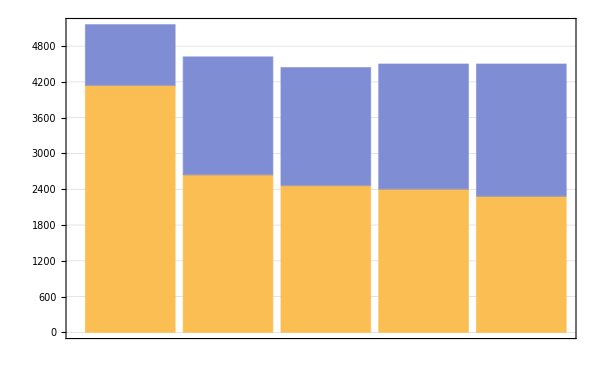

```mathematica
BarChart[{Take[differences,{1,2}],Take[differences,{3,4}],Take[differences,{5,6}],Take[differences,{7,8}],Take[differences,{9,10}]},
ChartLayout->"Stacked",
ImageSize->600,
Frame->True,
PlotTheme->"Detailed"]
```

```mathematica
d1={{0,1860,0},{1860,3720,5},{10000,11860,4},{15366,16806,9},{17822,19022,7},{21258,22278,0},{22568,23348,2},{26862,27642,3}};

d2={{0,1860,1},{1860,3720,6},{16680,17940,1},{18422,19502,3},{21590,22490,5},{27484,29224,8}};

d3={{0,1860,2},{1860,3720,7}};

d4={{0,1860,3},{1860,3720,8}};

d5={{0,1860,4},{1860,2880,9}};
```

```mathematica
d1=Take2[d1,1,2]
d2=Take2[d2,1,2]
d3=Take2[d3,1,2]
d4=Take2[d4,1,2]
d5=Take2[d5,1,2]
```

{{0,1860},{1860,3720},{10000,11860},{15366,16806},{17822,19022},{21258,22278},{22568,23348},{26862,27642}}

{{0,1860},{1860,3720},{16680,17940},{18422,19502},{21590,22490},{27484,29224}}

{{0,1860},{1860,3720}}

{{0,1860},{1860,3720}}

{{0,1860},{1860,2880}}

```mathematica
diffd1=Map[#[[2]]-#[[1]]&,d1];
diffd2=Map[#[[2]]-#[[1]]&,d2];
diffd3=Map[#[[2]]-#[[1]]&,d3];
diffd4=Map[#[[2]]-#[[1]]&,d4];
diffd5=Map[#[[2]]-#[[1]]&,d5];
```

```mathematica
getwaits[list_]:=Module[{i,waits={}},

For[i = 1, i <Length[list],i++,
AppendTo[waits,list[[i+1,1]]-list[[i,2]]];
];
Return[waits]
]
```

```mathematica
getbars[list1_,list2_]:=Module[{i,bars={}},

For[i=1, i< Length[list1],i++,

AppendTo[bars,list1[[i]]];
AppendTo[bars,list2[[i]]];
]
AppendTo[bars,list1[[Length[list1]]]];

Return[bars]
]
```

```mathematica
waitsd1=getwaits[d1]
waitsd2=getwaits[d2]
waitsd3=getwaits[d3]
waitsd4=getwaits[d4]
waitsd5=getwaits[d5]
```

{0,6280,3506,1016,2236,290,3514}

{0,12960,482,2088,4994}

{0}

{0}

{0}

```mathematica
barsd1=getbars[diffd1,waitsd1]
barsd2=getbars[diffd2,waitsd2]
barsd3=getbars[diffd3,waitsd3]
barsd4=getbars[diffd4,waitsd4]
barsd5=getbars[diffd5,waitsd5]
```

{1860,0,1860,6280,1860,3506,1440,1016,1200,2236,1020,290,780,3514,780}

{1860,0,1860,12960,1260,482,1080,2088,900,4994,1740}

{1860,0,1860}

{1860,0,1860}

{1860,0,1020}

```mathematica
color={};
For[i = 1, i< 15,i++,
AppendTo[color,Red];
AppendTo[color,White];
]
```

```mathematica
color
```

{RGBColor[1, 0, 0],GrayLevel[1],RGBColor[1, 0, 0],GrayLevel[1],RGBColor[1, 0, 0],GrayLevel[1],RGBColor[1, 0, 0],GrayLevel[1],RGBColor[1, 0, 0],GrayLevel[1],RGBColor[1, 0, 0],GrayLevel[1],RGBColor[1, 0, 0],GrayLevel[1],RGBColor[1, 0, 0],GrayLevel[1],RGBColor[1, 0, 0],GrayLevel[1],RGBColor[1, 0, 0],GrayLevel[1],RGBColor[1, 0, 0],GrayLevel[1],RGBColor[1, 0, 0],GrayLevel[1],RGBColor[1, 0, 0],GrayLevel[1],RGBColor[1, 0, 0],GrayLevel[1]}

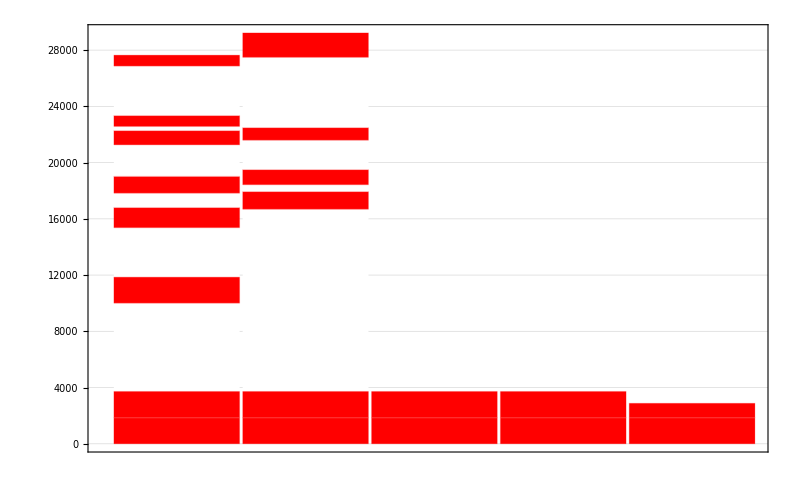

```mathematica
BarChart[{barsd1,barsd2,barsd3,barsd4,barsd5},
ChartLayout->"Stacked",
ImageSize->800,
Frame->True,
PlotTheme->"Detailed",
ChartStyle->color]
```

```mathematica
SetDirectory["/home/lindorfer/ReWiTech/Masterarbeit/Seminar/Vortrag/Simulations"]
```

/home/lindorfer/ReWiTech/Masterarbeit/Seminar/Vortrag/Simulations

#### Initial Solution

```mathematica
t1={{18600,0,18600,4866,18600,7376,4200,2576,2400,486,16800},{18600,0,18600,6280,12300,268,6000,9762,2400},{18600,0,18600,12960,9600},{18600,0,18600,14702,8700},{18600,0,6000,30138,6900}};
```

#### 500 Steps opt_2 Solution

```mathematica
t2={{0,2400,18600,0,6000,0,18600,0,18600,8538,2400},{16800,1800,18600,138,2400,1662,6900,8838,12300},{8700,0,18600,12110,18600,2292,6000},{4200,0,18600,13448,18600,56,18600},{9600,2700,18600,2700,18600,6660,2400}};
```

#### 500 Steps swap_2_difftrucks Solution

```mathematica
t3={{2400,0,18600,0,18600,9842,18600,-10984,6900,5708,2400},{18600,6360,18600,2320,6000,2858,16800},{18600,0,12300,6300,18600,2102,9600},{6000,0,18600},{18600,2210,8700,0,18600,14050,4200}};
```

```mathematica
lblStyle=Style[#,22,Black]&;
lblStyle/@{"Dock 1","Dock 2","Dock 3","Dock 4","Dock 5"}
```

{Dock 1,Dock 2,Dock 3,Dock 4,Dock 5}

```mathematica
Table["Dock "<>ToString[i],{i,1,5}]
```

{Dock 1,Dock 2,Dock 3,Dock 4,Dock 5}

```mathematica
PlotBarChart[list_,max_,ndocks_:5,imgsize_:700,linestart_:0.34,color_:color,type_:"Dock",xrange_:All]:=BarChart[list,
ChartLayout->"Stacked",
ChartLabels->{lblStyle/@Table[type <>ToString[i],{i,1,ndocks}],None},
FrameLabel->{"","time / sec"},
LabelStyle->{22,Black,Italic},
ImageSize->imgsize,
Frame->True,
FrameStyle->Directive[Thickness[0.002]],
PlotTheme->"Detailed",
ChartStyle->color,
PlotRange->{xrange,{0,max}},
Epilog->{Black,{Thickness[0.01],Line[{{linestart,max},{100,max}}]}}
(*,ChartLegends->Placed[SwatchLegend[{Black},{"Latest Return-Time"},LegendMarkers->"Line",LegendMarkerSize->20],Top]*)
]
```

Barchart Tries

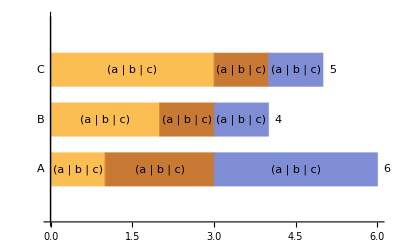

```mathematica
BarChart[#,BarOrigin->Left,ChartLayout->"Stacked",BarSpacing->0.5,ChartLabels->{Placed[{{"A","B","C"},Total@#},{Before,After}],None},LabelingFunction->(Placed[{{"a","b","c"}},Center]&)]&@{{1,2,3},{2,1,1},{3,1,1}}
```

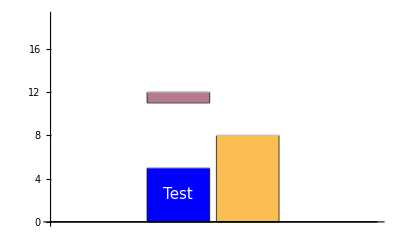

```mathematica
BarChart[{{Style[Labeled[5,Style["Test",White, 15],Center],Blue],6,1,7},{8,8}},ChartLayout->"Stacked",ChartStyle->{EdgeForm[{Thick,Black}],White}]
```

```mathematica
ColorData["BrightBands"]
```

ColorDataFunction[…]

```mathematica
ColorData["BrightBands",0.5]
```

RGBColor[0.23499123809468608, 0.9676036067435916, 0.1156329799245431]

```mathematica
ToCallout[list_]:=Module[{clist={},i},
For[i = 1, i ≤Length[list],i++,
AppendTo[clist,Callout[list[[i]],"test"<>ToString[i]]];
];
Return[clist]
]
```

```mathematica
Map[ToCallout[#]&,{{5,6,7,5,7},{8,5,6,7,8}}]
```

{{Callout[5,test1],Callout[6,test2],Callout[7,test3],Callout[5,test4],Callout[7,test5]},{Callout[8,test1],Callout[5,test2],Callout[6,test3],Callout[7,test4],Callout[8,test5]}}

```mathematica
Table[Callout[RandomReal[{0,1}],Unique["text"]],2,8]
```

{{Callout[0.0693602,text135],Callout[0.835978,text136],Callout[0.117955,text137],Callout[0.198372,text138],Callout[0.0233509,text139],Callout[0.338659,text140],Callout[0.0610752,text141],Callout[0.731896,text142]},{Callout[0.658665,text143],Callout[0.820276,text144],Callout[0.708214,text145],Callout[0.276857,text146],Callout[0.620679,text147],Callout[0.194003,text148],Callout[0.755631,text149],Callout[0.44847,text150]}}

```mathematica
BarChart[Map[ToCallout[#]&,{{5,6,7,5,7},{8,5,6,7,8}}],BarSpacing->2,ChartLayout->"Stacked"]
```

-Graphics-

```mathematica
BarChart[Table[Callout[RandomReal[{0,1}],Unique["text"]],2,8],BarSpacing->2,ChartLayout->"Stacked"]
```

-Graphics-

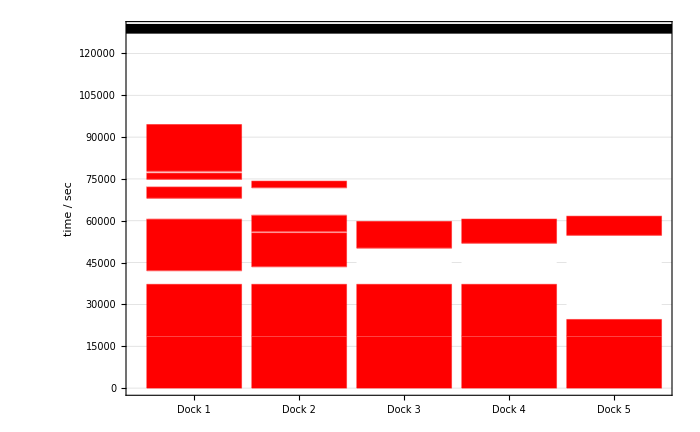

```mathematica
init=PlotBarChart[t1,128842,5,700,0.34]
```

```mathematica
t1labels={{Style[Labeled[18600,Style["Truck 1",Black,12],Center],ColorData["BrightBands",0]],0,Style[Labeled[18600,Style["Truck 6",Black,12],Center],ColorData["BrightBands",0.5]],4866,Style[Labeled[18600,Style["Truck 10",Black,12],Center],ColorData["BrightBands",0.9]],7376,Style[Labeled[4200,Style["Truck 8",Black,12],Center],ColorData["BrightBands",0.7]],2576,Style[Labeled[2400,Style["Truck 1",Black,12],Center],ColorData["BrightBands",0]],486,Style[Labeled[16800,Style["Truck 9",Black,12],Center],ColorData["BrightBands",0.8]]},{Style[Labeled[18600,Style["Truck 2",Black,12],Center],ColorData["BrightBands",0.1]],0,Style[Labeled[18600,Style["Truck 7",Black,12],Center],ColorData["BrightBands",0.6]],6280,Style[Labeled[12300,Style["Truck 5",Black,12],Center],ColorData["BrightBands",0.4]],268,Style[Labeled[6000,Style["Truck 3",Black,12],Center],ColorData["BrightBands",0.2]],9762,Style[Labeled[2400,Style["Truck 6",Black,12],Center],ColorData["BrightBands",0.5]]},{Style[Labeled[18600,Style["Truck 3",Black,12],Center],ColorData["BrightBands",0.2]],0,Style[Labeled[18600,Style["Truck 8",Black,12],Center],ColorData["BrightBands",0.7]],12960,Style[Labeled[9600,Style["Truck 2",Black,12],Center],ColorData["BrightBands",0.1]]},{Style[Labeled[18600,Style["Truck 4",Black,12],Center],ColorData["BrightBands",0.3]],0,Style[Labeled[18600,Style["Truck 9",Black,12],Center],ColorData["BrightBands",0.8]],14702,Style[Labeled[8700,Style["Truck 4",Black,12],Center],ColorData["BrightBands",0.3]]},{Style[Labeled[18600,Style["Truck 5",Black,12],Center],ColorData["BrightBands",0.4]],0,Style[Labeled[6000,Style["Truck 10",Black,12],Center],ColorData["BrightBands",0.9]],30138,Style[Labeled[6900,Style["Truck 1",Black,12],Center],ColorData["BrightBands",0]]}};
```

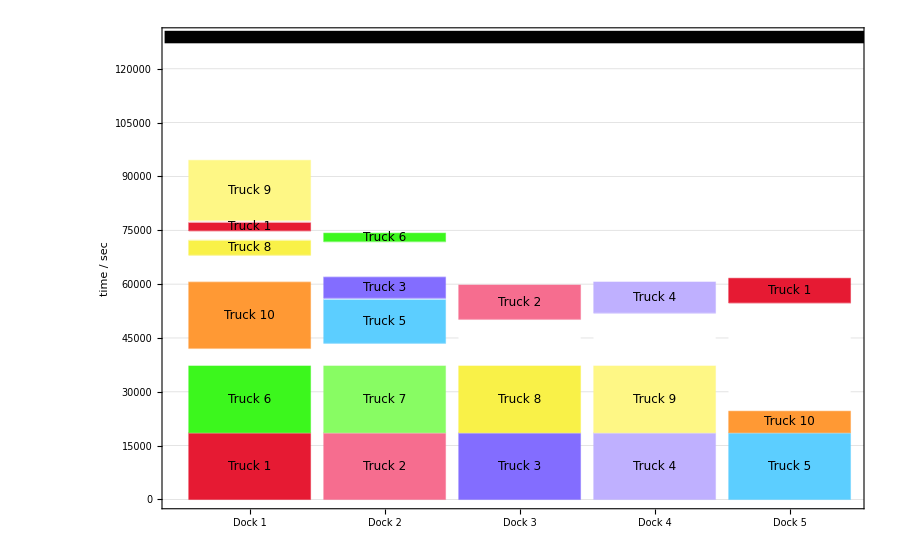

```mathematica
init=PlotBarChart[t1labels,128842,5,900,0.37,color]
```

## Plot Trucks

```mathematica
trucks={{Style[Labeled[54738,Style["Job 0",Black,12],Center],Lighter[ColorData["Rainbow",0]]],0,Style[Labeled[20080,Style["Job 4",Black,12],Center],Lighter[ColorData["Rainbow",0.4]]],0,Style[Labeled[26704,Style["Job 8",Black,12],Center],Lighter[ColorData["Rainbow",0.8]]]},{Style[Labeled[50160,Style["Job 1",Black,12],Center],Lighter[ColorData["Rainbow",0.1]]],0,Style[Labeled[38048,Style["Job 2",Black,12],Center],Lighter[ColorData["Rainbow",0.2]]]},{Style[Labeled[56048,Style["Job 2",Black,12],Center],Lighter[ColorData["Rainbow",0.2]]],0,Style[Labeled[28010,Style["Job 5",Black,12],Center],Lighter[ColorData["Rainbow",0.5]]]},{Style[Labeled[51902,Style["Job 3",Black,12],Center],Lighter[ColorData["Rainbow",0.3]]],0,Style[Labeled[32102,Style["Job 3",Black,12],Center],Lighter[ColorData["Rainbow",0.3]]]},{Style[Labeled[43480,Style["Job 4",Black,12],Center],Lighter[ColorData["Rainbow",0.4]]],0,Style[Labeled[37560,Style["Job 1",Black,12],Center],Lighter[ColorData["Rainbow",0.1]]]},{0,18600,Style[Labeled[53210,Style["Job 5",Black,12],Center],Lighter[ColorData["Rainbow",0.5]]],0,Style[Labeled[17042,Style["Job 7",Black,12],Center],Lighter[ColorData["Rainbow",0.7]]]},{0,18600,Style[Labeled[62330,Style["Job 6",Black,12],Center],Lighter[ColorData["Rainbow",0.6]]]},{0,18600,Style[Labeled[49442,Style["Job 7",Black,12],Center],Lighter[ColorData["Rainbow",0.7]]],0,Style[Labeled[33530,Style["Job 6",Black,12],Center],Lighter[ColorData["Rainbow",0.6]]]},{0,18600,Style[Labeled[59104,Style["Job 8",Black,12],Center],Lighter[ColorData["Rainbow",0.8]]],0,Style[Labeled[51138,Style["Job 0",Black,12],Center],Lighter[ColorData["Rainbow",0]]]},{0,18600,Style[Labeled[23466,Style["Job 9",Black,12],Center],Lighter[ColorData["Rainbow",0.9]]],0,Style[Labeled[54738,Style["Job 0",Black,12],Center],Lighter[ColorData["Rainbow",0]]]}};
```

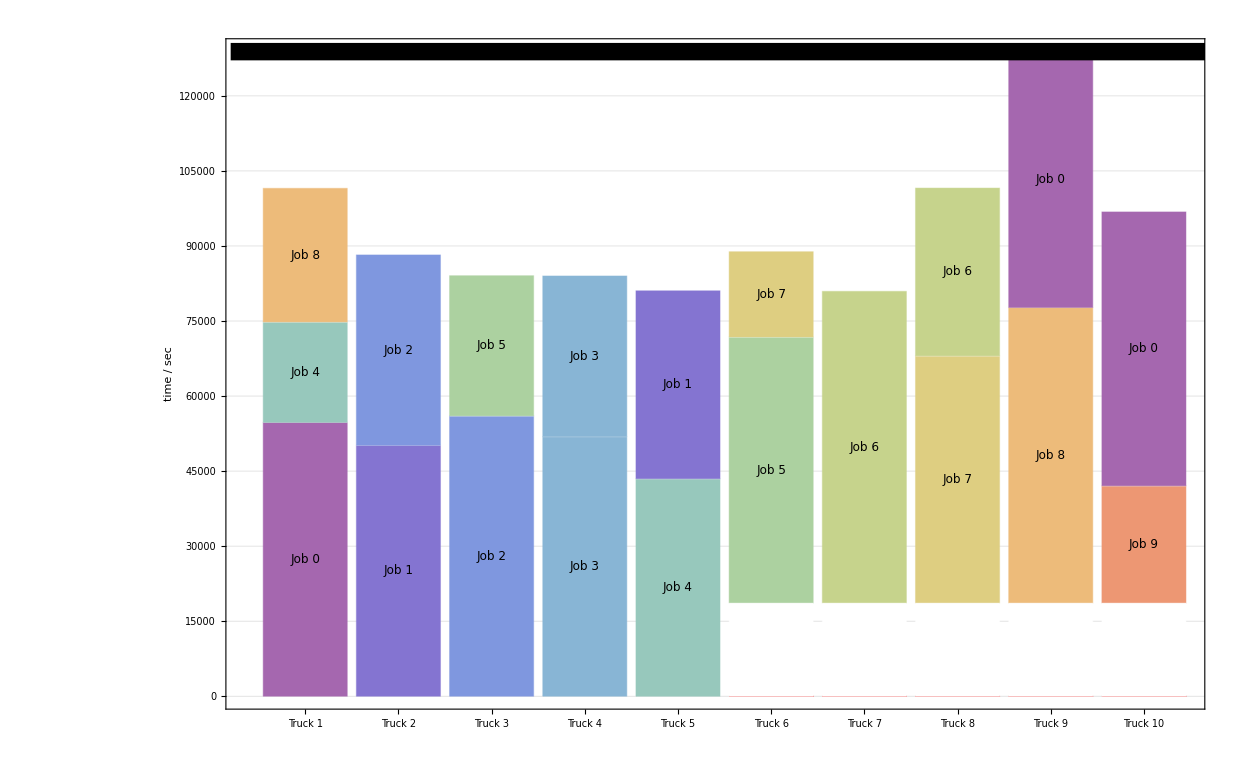

```mathematica
PlotBarChart[trucks,128842,10,1000,0.2,color, "Truck "]
```

```mathematica
93/128//N
```

0.726563

```mathematica
Export["init_sol.jpeg",init]
```

init_sol.jpeg

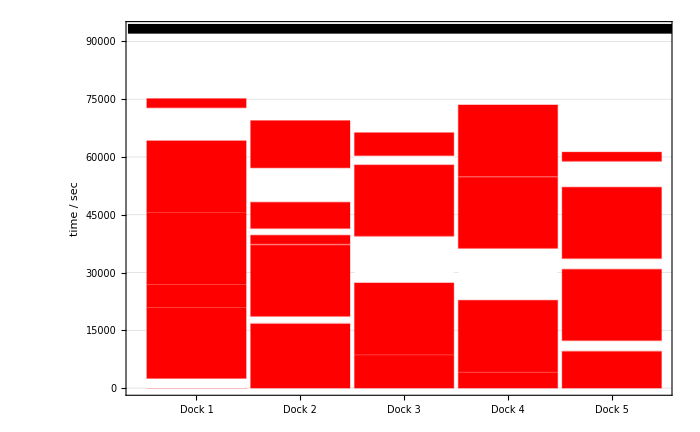

```mathematica
opt2500=PlotBarChart[t2,93272]
```

```mathematica
Export["opt2500_sol.jpeg",opt2500]
```

opt2500_sol.jpeg

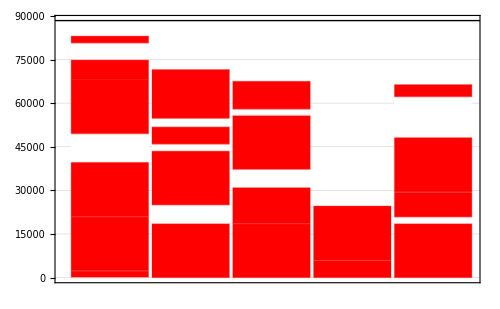

```mathematica
PlotBarChart[t3,88396]
```

#### Initial Solution

```mathematica
t1={{18600,0,18600,4866,18600,7376,4200,2576,2400,486,16800},{18600,0,18600,6280,12300,268,6000,9762,2400},{18600,0,18600,12960,9600},{18600,0,18600,14702,8700},{18600,0,6000,30138,6900}};
```

#### 500 Steps opt_2 + 50 swap2 + 500 opt_2 Solution

```mathematica
t2={{2400,0,4200,0,2400,0,6000,7800,18600,4500,6000,2304,18600},{18600,4266,6900,7076,18600},{18600,6902,18600,4564,18600},{8700,0,18600,6660,18600,2400,9600},{12300,8510,16800,3856,18600}};
```

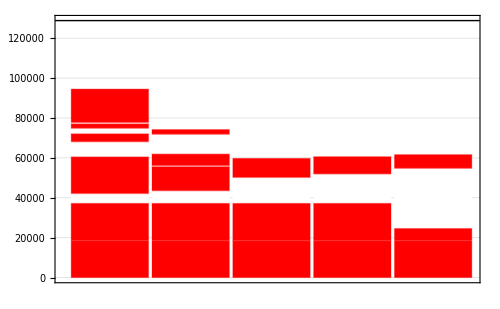

```mathematica
PlotBarChart[t1,128842]
```

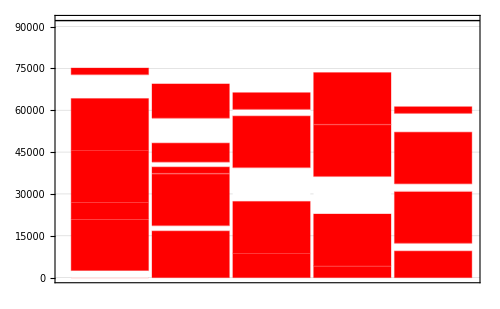

```mathematica
PlotBarChart[t2,92146]
```

```mathematica
t3={{2400,16200,18600,0,18600,0,18600},{6000,0,9600,666,6900,0,12300,0,18600,672,18600},{6000,0,16800,0,18600,242,18600,14460,4200},{18600,21000,8700,366,18600},{18600,44702,2400}};
PlotBarChart[t2,92146]
```

```mathematica
einf={{5000,2000,5000},{0,4000,1200,0}}
```

{{5000,2000,5000},{0,4000,1200,0}}

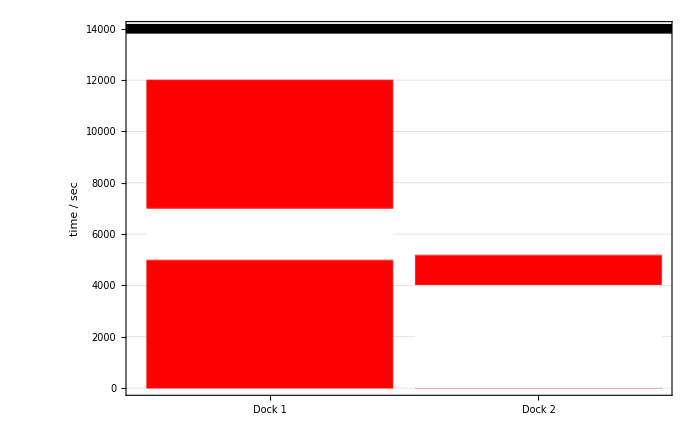

```mathematica
einfplot=PlotBarChart[einf,14000]
```

```mathematica
Export["einfplot.jpeg",einfplot]
```

einfplot.jpeg

```mathematica
vnssol={{2400,3600,18600,11648,18600,0,6000,8154,2400},{6900,0,18600,8404,18600},{18600,0,18600,8700,4200,5466,9600},{8700,0,18600,0,18600,0,12300},{6000,0,18600,6738,18600,0,16800}};
```

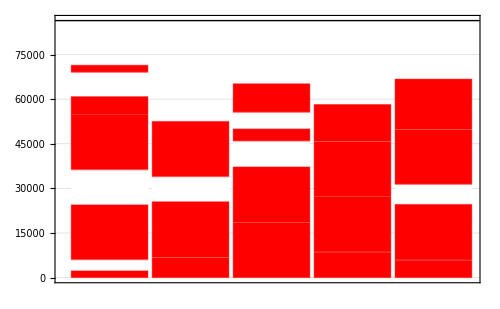

```mathematica
PlotBarChart[vnssol,86408]
```

```mathematica
vnssol2={{6000,0,2400,0,18600,0,18600,3066,16800},{18600,2210,12300,794,18600,7606,4200},{2400,0,18600,16200,18600},{6900,0,18600,5838,18600,8622,6000},{18600,3666,18600,5014,8700,3072,9600}};
```

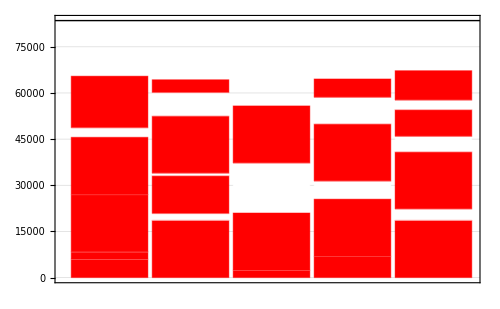

```mathematica
PlotBarChart[vnssol2,83520]
```

```mathematica
vnssol3={{6000,0,2400,0,18600,0,18600,3066,16800},{18600,2210,12300,794,18600,7606,4200},{2400,0,18600,16200,18600},{6900,0,18600,5838,18600,8622,6000},{18600,3666,18600,5014,8700,3072,9600}};
PlotBarChart[vnssol3,83520]
```

-Graphics-

```mathematica
vnssol4={{6000,0,2400,0,18600,0,18600,690,12300},{18600,2210,9600,6790,8700,0,18600},{2400,0,18600,12904,18600,6056,6000},{6900,0,18600,5838,18600,10172,4200},{18600,3666,18600,7800,16800}}
```

{{6000,0,2400,0,18600,0,18600,690,12300},{18600,2210,9600,6790,8700,0,18600},{2400,0,18600,12904,18600,6056,6000},{6900,0,18600,5838,18600,10172,4200},{18600,3666,18600,7800,16800}}

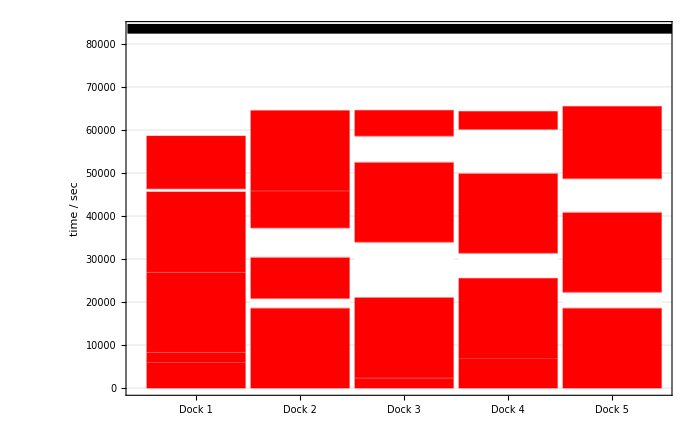

```mathematica
vnssolplot=PlotBarChart[vnssol4,83520]
```

```mathematica
Export["vns_sol.jpeg",vnssolplot]
```

vns_sol.jpeg

### Increase Docksize from 5 to 6

```mathematica
vnssol5={{6900,0,18600,13868,8700,13570,2400},{2400,0,18600,0,18600,3600,18600},{6000,0,18600,360,18600,2320,12300},{18600,12738,18600},{18600,30842,16800},{9600,6666,4200,5014,18600,4586,6000}};
```

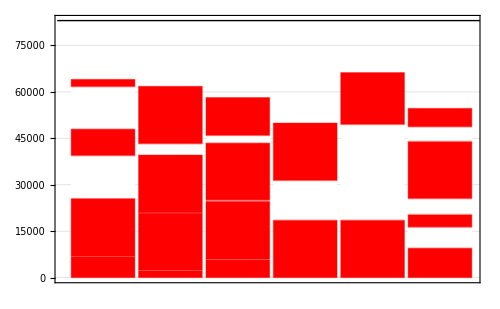

```mathematica
PlotBarChart[vnssol5,83042]
```

### Increase Docksize from 5 to 8

```mathematica
vnssol6={{18600,2210,4200},{2400,0,9600,4266,18600,1976,18600},{2400,3600,18600,19312,18600},{18600,18600,8700},{12300,15580,18600,2962,16800},{18600,30066,6000},{18600,36138,6000},{18600,31560,6900}};
```

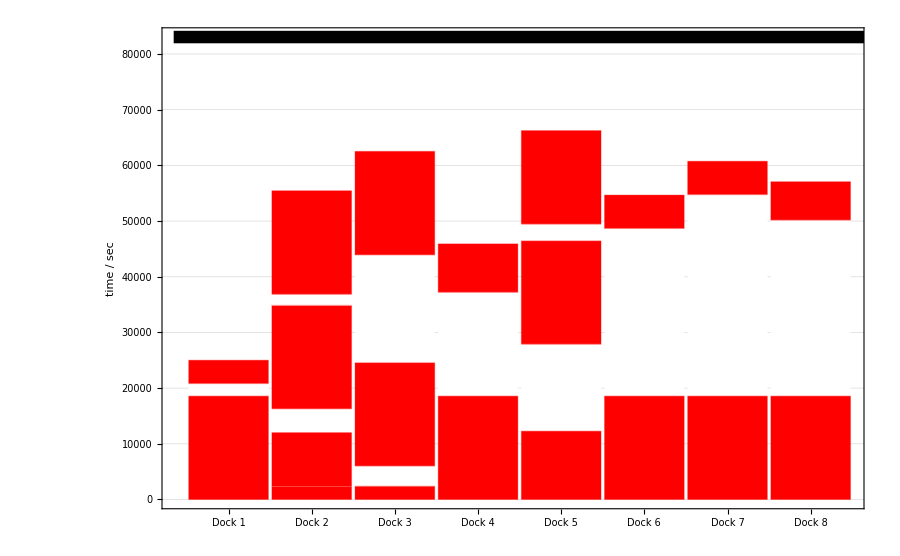

```mathematica
vnssol8plot=PlotBarChart[vnssol6,83042,8,900]
```

```mathematica
Export["vns8_sol.jpeg",vnssol8plot]
```

vns8_sol.jpeg

### Increase Docksize from 5 to 10

```mathematica
vnssol7={{18600,6360,18600},{6000,37480,6000},{18600,30066,6900},{18600,24880,8700},{18600,15000,18600,1010,2400,438,2400},{18600,18242,18600},{18600,31560,4200},{18600},{16800,35102,9600},{12300}};
```

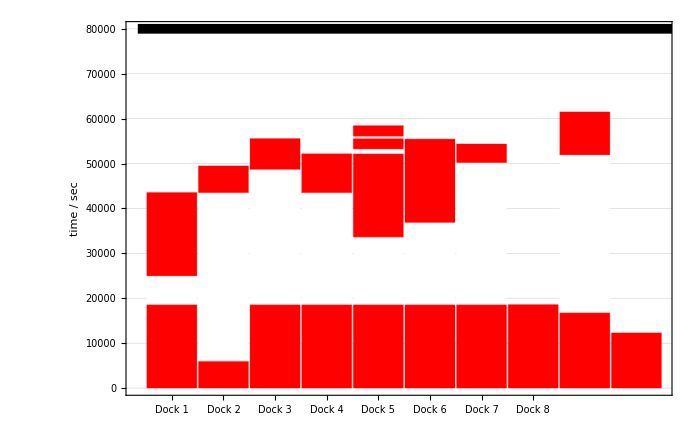

```mathematica
PlotBarChart[vnssol7,80004,8]
```

```mathematica
vnssol8={{18600,2210,18600,16638,2400},{9600,15880,18600},{2400,22560,18600},{4200,18902,18600},{18600,18600,18600},{6000,37480,16800},{18600,15304,12300},{18600,12738,18600},{6000,37480,8700},{6900}};
```

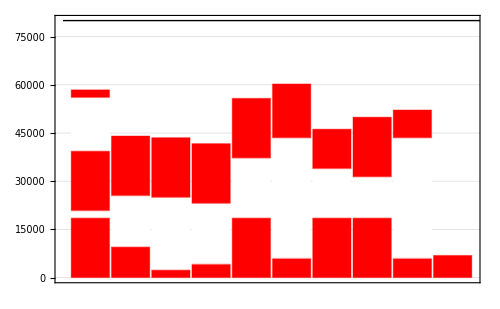

```mathematica
PlotBarChart[vnssol8,80004]
```

### Decrease Docksize from 5 to 2

```mathematica
initsol={{18600,0,18600,0,18600,0,18600,0,18600,0,12300,0,8700,0,6000,0,2400,6280,16800},{18600,0,18600,0,18600,0,18600,0,6000,0,18600,0,9600,0,6900,0,4200,0,2400}};
```

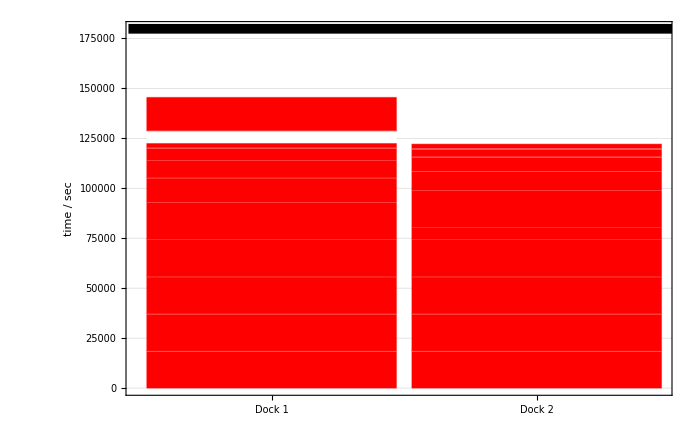

```mathematica
PlotBarChart[initsol,179818,2,700,0.46]
```

```mathematica
vnss2={{18600,0,18600,0,18600,0,18600,0,6000,0,18600,0,8700,0,6000,0,4200,0,2400,0,9600},{18600,0,6900,0,18600,0,18600,0,18600,0,18600,0,12300,0,16800,0,2400}};
```

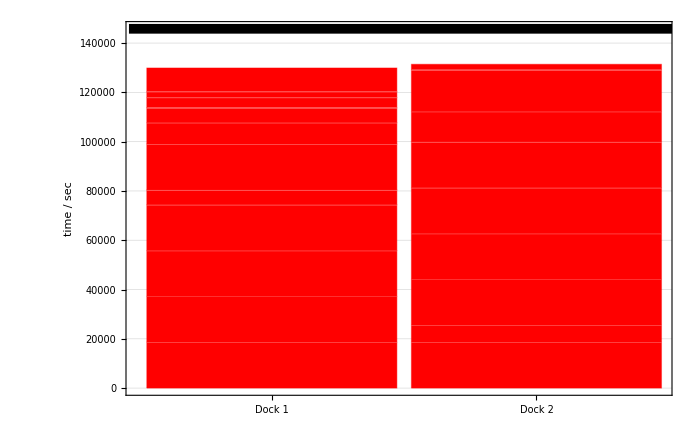

```mathematica
PlotBarChart[vnss2,145800,2,700,0.46]
```

### Decrease Docksize from 5 to 3

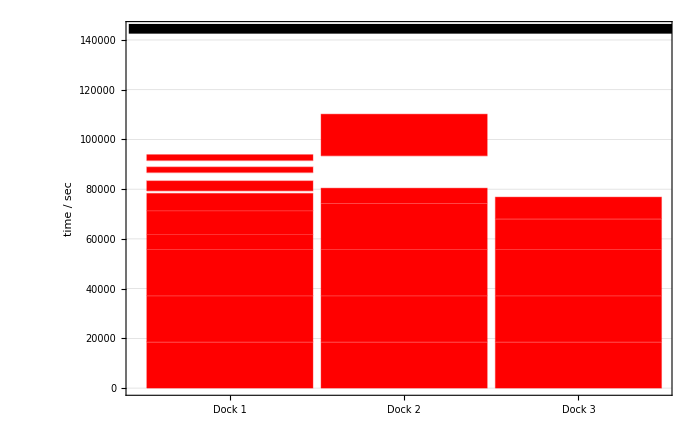

```mathematica
initsol3={{18600,0,18600,0,18600,0,6000,0,9600,0,6900,966,4200,3176,2400,2438,2400},{18600,0,18600,0,18600,0,18600,0,6000,12960,16800},{18600,0,18600,0,18600,0,12300,0,8700}};
d3init=PlotBarChart[initsol3,144498,3,700,0.42]
```

```mathematica
vnssol3={{6000,0,4200,0,18600,0,18600,0,18600,0,18600,0,2400},{18600,0,18600,0,18600,0,2400,0,12300,0,6900,0,9600},{18600,0,18600,0,6000,0,18600,0,8700,0,16800}};
```

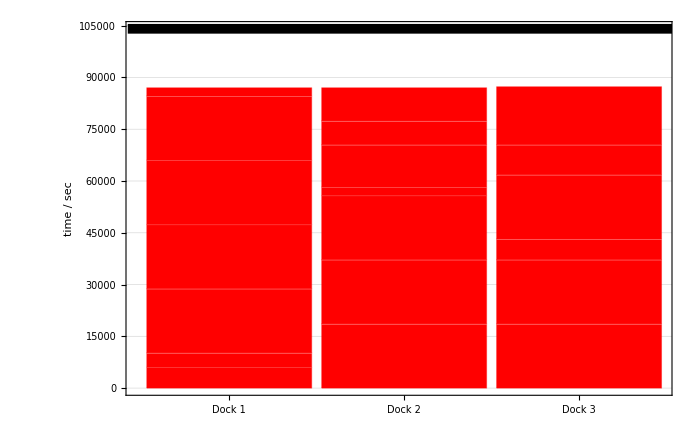

```mathematica
d3vns=PlotBarChart[vnssol3,104100,3,700,0.42]
```

```mathematica
Export["initd3_sol.jpeg",d3init]
Export["vnsd3_sol.jpeg",d3vns]
```

initd3_sol.jpeg

vnsd3_sol.jpeg

### Decrease Docksize from 5 to 4

```mathematica
initsol4={{18600,0,18600,0,18600,248,8700,3294,4200,8688,2400,952,16800},{18600,0,18600,0,6000,6960,18600,3050,2400},{18600,0,18600,14702,12300,0,6900},{18600,0,18600,17538,9600,0,6000}};
```

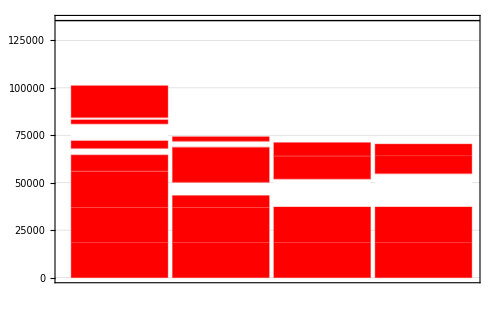

```mathematica
PlotBarChart[initsol4,135420]
```

```mathematica
vnssol4={{2400,0,18600,0,18600,0,18600,2402,9600},{8700,0,18600,6604,18600,0,16800},{6000,0,18600,0,6000,738,18600,0,12300},{6900,0,18600,0,18600,0,18600,0,4200,3542,2400}};
```

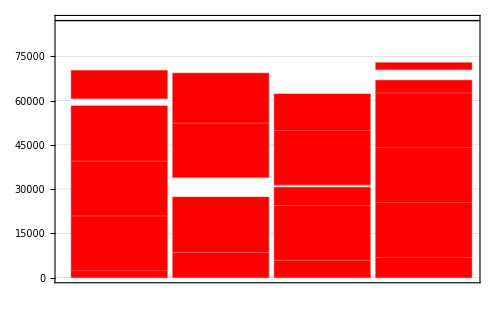

```mathematica
PlotBarChart[vnssol4,87114]
```

#### Results for 5 - Level VND/S with colored Jobs and Truck Plots

Initial Solution

```mathematica
t1labels={{Style[Labeled[18600,Style["Truck 1",Black,12],Center],ColorData["BrightBands",0]],0,Style[Labeled[18600,Style["Truck 6",Black,12],Center],ColorData["BrightBands",0.5]],4866,Style[Labeled[18600,Style["Truck 10",Black,12],Center],ColorData["BrightBands",0.9]],7376,Style[Labeled[4200,Style["Truck 8",Black,12],Center],ColorData["BrightBands",0.7]],2576,Style[Labeled[2400,Style["Truck 1",Black,12],Center],ColorData["BrightBands",0]],486,Style[Labeled[16800,Style["Truck 9",Black,12],Center],ColorData["BrightBands",0.8]]},{Style[Labeled[18600,Style["Truck 2",Black,12],Center],ColorData["BrightBands",0.1]],0,Style[Labeled[18600,Style["Truck 7",Black,12],Center],ColorData["BrightBands",0.6]],6280,Style[Labeled[12300,Style["Truck 5",Black,12],Center],ColorData["BrightBands",0.4]],268,Style[Labeled[6000,Style["Truck 3",Black,12],Center],ColorData["BrightBands",0.2]],9762,Style[Labeled[2400,Style["Truck 6",Black,12],Center],ColorData["BrightBands",0.5]]},{Style[Labeled[18600,Style["Truck 3",Black,12],Center],ColorData["BrightBands",0.2]],0,Style[Labeled[18600,Style["Truck 8",Black,12],Center],ColorData["BrightBands",0.7]],12960,Style[Labeled[9600,Style["Truck 2",Black,12],Center],ColorData["BrightBands",0.1]]},{Style[Labeled[18600,Style["Truck 4",Black,12],Center],ColorData["BrightBands",0.3]],0,Style[Labeled[18600,Style["Truck 9",Black,12],Center],ColorData["BrightBands",0.8]],14702,Style[Labeled[8700,Style["Truck 4",Black,12],Center],ColorData["BrightBands",0.3]]},{Style[Labeled[18600,Style["Truck 5",Black,12],Center],ColorData["BrightBands",0.4]],0,Style[Labeled[6000,Style["Truck 10",Black,12],Center],ColorData["BrightBands",0.9]],30138,Style[Labeled[6900,Style["Truck 1",Black,12],Center],ColorData["BrightBands",0]]}};
```

```mathematica
init=PlotBarChart[t1labels,128842,5,900,0.37,color]
```

-Graphics-

```mathematica
truckst1={{Style[Labeled[54738,Style["Job 0",Black,12],Center],Lighter[ColorData["Rainbow",0]]],0,Style[Labeled[20080,Style["Job 4",Black,12],Center],Lighter[ColorData["Rainbow",0.4]]],0,Style[Labeled[26704,Style["Job 8",Black,12],Center],Lighter[ColorData["Rainbow",0.8]]]},{Style[Labeled[50160,Style["Job 1",Black,12],Center],Lighter[ColorData["Rainbow",0.1]]],0,Style[Labeled[38048,Style["Job 2",Black,12],Center],Lighter[ColorData["Rainbow",0.2]]]},{Style[Labeled[56048,Style["Job 2",Black,12],Center],Lighter[ColorData["Rainbow",0.2]]],0,Style[Labeled[28010,Style["Job 5",Black,12],Center],Lighter[ColorData["Rainbow",0.5]]]},{Style[Labeled[51902,Style["Job 3",Black,12],Center],Lighter[ColorData["Rainbow",0.3]]],0,Style[Labeled[32102,Style["Job 3",Black,12],Center],Lighter[ColorData["Rainbow",0.3]]]},{Style[Labeled[43480,Style["Job 4",Black,12],Center],Lighter[ColorData["Rainbow",0.4]]],0,Style[Labeled[37560,Style["Job 1",Black,12],Center],Lighter[ColorData["Rainbow",0.1]]]},{0,18600,Style[Labeled[53210,Style["Job 5",Black,12],Center],Lighter[ColorData["Rainbow",0.5]]],0,Style[Labeled[17042,Style["Job 7",Black,12],Center],Lighter[ColorData["Rainbow",0.7]]]},{0,18600,Style[Labeled[62330,Style["Job 6",Black,12],Center],Lighter[ColorData["Rainbow",0.6]]]},{0,18600,Style[Labeled[49442,Style["Job 7",Black,12],Center],Lighter[ColorData["Rainbow",0.7]]],0,Style[Labeled[33530,Style["Job 6",Black,12],Center],Lighter[ColorData["Rainbow",0.6]]]},{0,18600,Style[Labeled[59104,Style["Job 8",Black,12],Center],Lighter[ColorData["Rainbow",0.8]]],0,Style[Labeled[51138,Style["Job 0",Black,12],Center],Lighter[ColorData["Rainbow",0]]]},{0,18600,Style[Labeled[23466,Style["Job 9",Black,12],Center],Lighter[ColorData["Rainbow",0.9]]],0,Style[Labeled[54738,Style["Job 0",Black,12],Center],Lighter[ColorData["Rainbow",0]]]}};
```

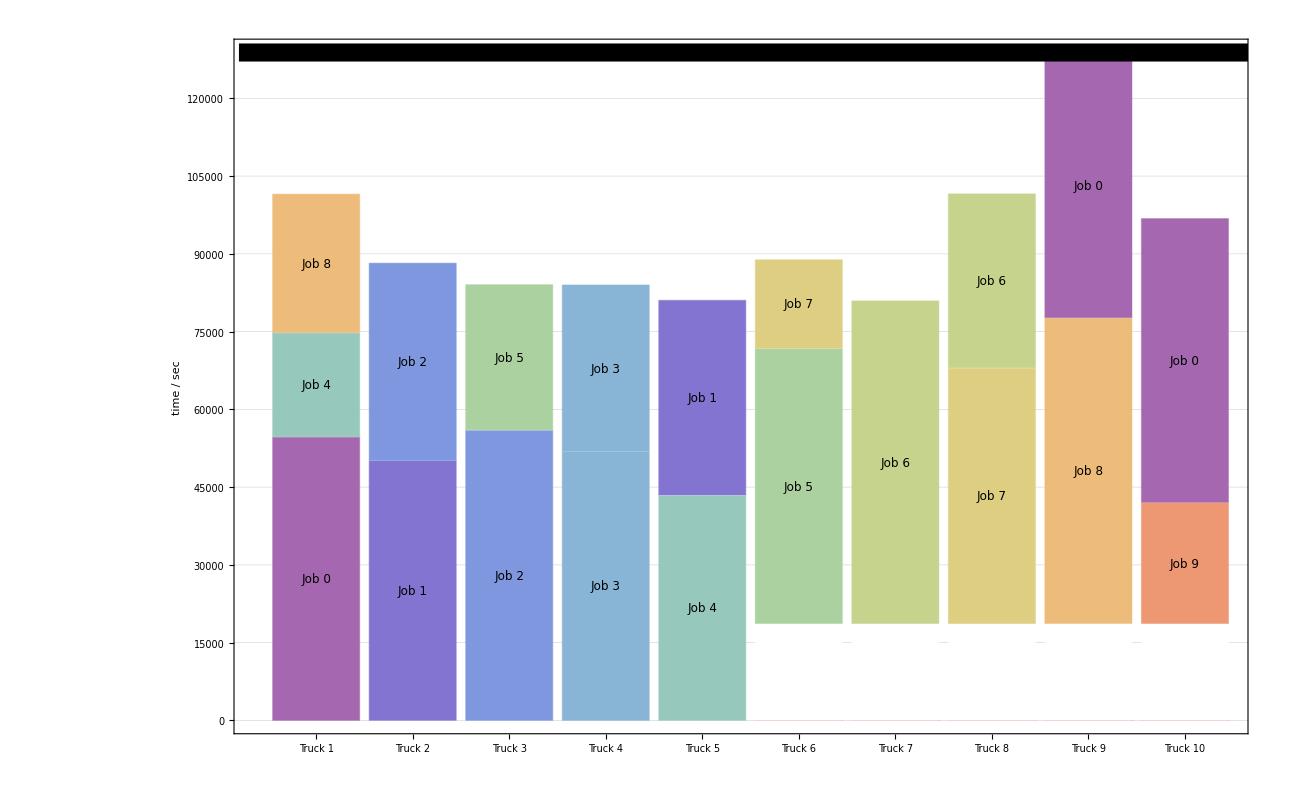

```mathematica
inittrucks=PlotBarChart[truckst1,128842,10,1300,0.2,color, "Truck "]
```

5 Docks: VNDS Optimization with 1000 nsteps && 100 moves

```mathematica
d5={{Style[Labeled[6000,Style["Truck 10",Black,12],Center],ColorData["BrightBands",0.9]],0,Style[Labeled[18600,Style["Truck 6",Black,12],Center],ColorData["BrightBands",0.5]],0,Style[Labeled[18600,Style["Truck 7",Black,12],Center],ColorData["BrightBands",0.6]],2700,Style[Labeled[16800,Style["Truck 8",Black,12],Center],ColorData["BrightBands",0.7]]},{Style[Labeled[8700,Style["Truck 5",Black,12],Center],ColorData["BrightBands",0.4]],0,Style[Labeled[18600,Style["Truck 8",Black,12],Center],ColorData["BrightBands",0.7]],0,Style[Labeled[18600,Style["Truck 4",Black,12],Center],ColorData["BrightBands",0.3]],4480,Style[Labeled[6000,Style["Truck 3",Black,12],Center],ColorData["BrightBands",0.2]]},{Style[Labeled[12300,Style["Truck 9",Black,12],Center],ColorData["BrightBands",0.8]],0,Style[Labeled[18600,Style["Truck 2",Black,12],Center],ColorData["BrightBands",0.1]],438,Style[Labeled[2400,Style["Truck 1",Black,12],Center],ColorData["BrightBands",0]],3104,Style[Labeled[18600,Style["Truck 9",Black,12],Center],ColorData["BrightBands",0.8]],3768,Style[Labeled[2400,Style["Truck 6",Black,12],Center],ColorData["BrightBands",0.5]],850,Style[Labeled[4200,Style["Truck 2",Black,12],Center],ColorData["BrightBands",0.1]]},{Style[Labeled[9600,Style["Truck 4",Black,12],Center],ColorData["BrightBands",0.3]],15360,Style[Labeled[18600,Style["Truck 10",Black,12],Center],ColorData["BrightBands",0.9]],4044,Style[Labeled[18600,Style["Truck 1",Black,12],Center],ColorData["BrightBands",0]]},{Style[Labeled[6900,Style["Truck 1",Black,12],Center],ColorData["BrightBands",0]],0,Style[Labeled[18600,Style["Truck 3",Black,12],Center],ColorData["BrightBands",0.2]],10748,Style[Labeled[18600,Style["Truck 5",Black,12],Center],ColorData["BrightBands",0.4]]}};
t5={{Style[Labeled[31338,Style["Job 4",Black,12],Center],Lighter[ColorData["Rainbow",0.4]]],0,Style[Labeled[16266,Style["Job 8",Black,12],Center],Lighter[ColorData["Rainbow",0.8]]],0,Style[Labeled[37200,Style["Job 0",Black,12],Center],Lighter[ColorData["Rainbow",0]]]},{0,12300,Style[Labeled[50160,Style["Job 5",Black,12],Center],Lighter[ColorData["Rainbow",0.5]]],0,Style[Labeled[23102,Style["Job 6",Black,12],Center],Lighter[ColorData["Rainbow",0.6]]]},{0,6900,Style[Labeled[43480,Style["Job 2",Black,12],Center],Lighter[ColorData["Rainbow",0.2]]],0,Style[Labeled[33904,Style["Job 9",Black,12],Center],Lighter[ColorData["Rainbow",0.9]]]},{Style[Labeled[25480,Style["Job 2",Black,12],Center],Lighter[ColorData["Rainbow",0.2]]],1820,Style[Labeled[54738,Style["Job 4",Black,12],Center],Lighter[ColorData["Rainbow",0.4]]]},{Style[Labeled[36248,Style["Job 3",Black,12],Center],Lighter[ColorData["Rainbow",0.3]]],0,Style[Labeled[49442,Style["Job 1",Black,12],Center],Lighter[ColorData["Rainbow",0.1]]]},{0,6000,Style[Labeled[53210,Style["Job 7",Black,12],Center],Lighter[ColorData["Rainbow",0.7]]],0,Style[Labeled[20810,Style["Job 7",Black,12],Center],Lighter[ColorData["Rainbow",0.7]]]},{0,24600,Style[Labeled[51902,Style["Job 6",Black,12],Center],Lighter[ColorData["Rainbow",0.6]]]},{0,8700,Style[Labeled[37200,Style["Job 0",Black,12],Center],Lighter[ColorData["Rainbow",0]]],0,Style[Labeled[33600,Style["Job 0",Black,12],Center],Lighter[ColorData["Rainbow",0]]]},{Style[Labeled[36842,Style["Job 1",Black,12],Center],Lighter[ColorData["Rainbow",0.1]]],0,Style[Labeled[48666,Style["Job 8",Black,12],Center],Lighter[ColorData["Rainbow",0.8]]]},{Style[Labeled[24960,Style["Job 5",Black,12],Center],Lighter[ColorData["Rainbow",0.5]]],0,Style[Labeled[56048,Style["Job 3",Black,12],Center],Lighter[ColorData["Rainbow",0.3]]]}};
```

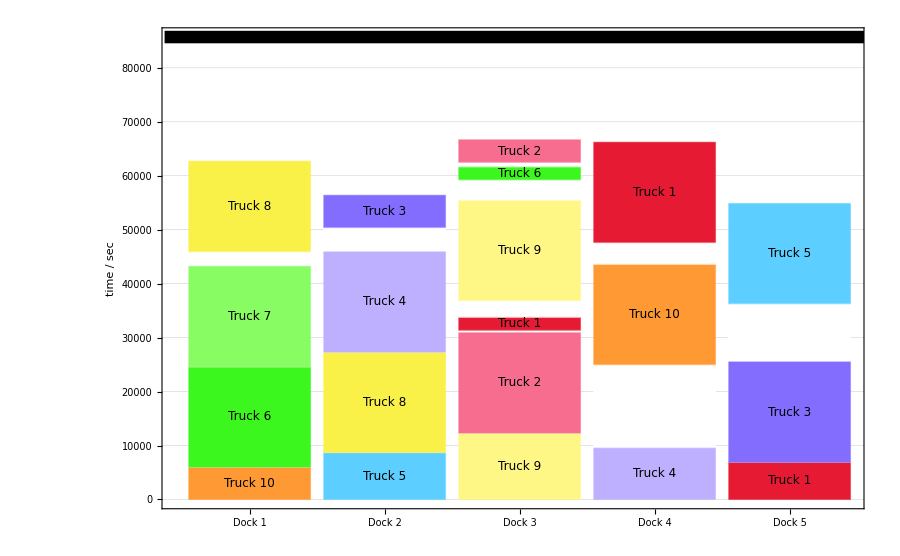

```mathematica
d5opt=PlotBarChart[d5,85690,5,900,0.37,color]
```

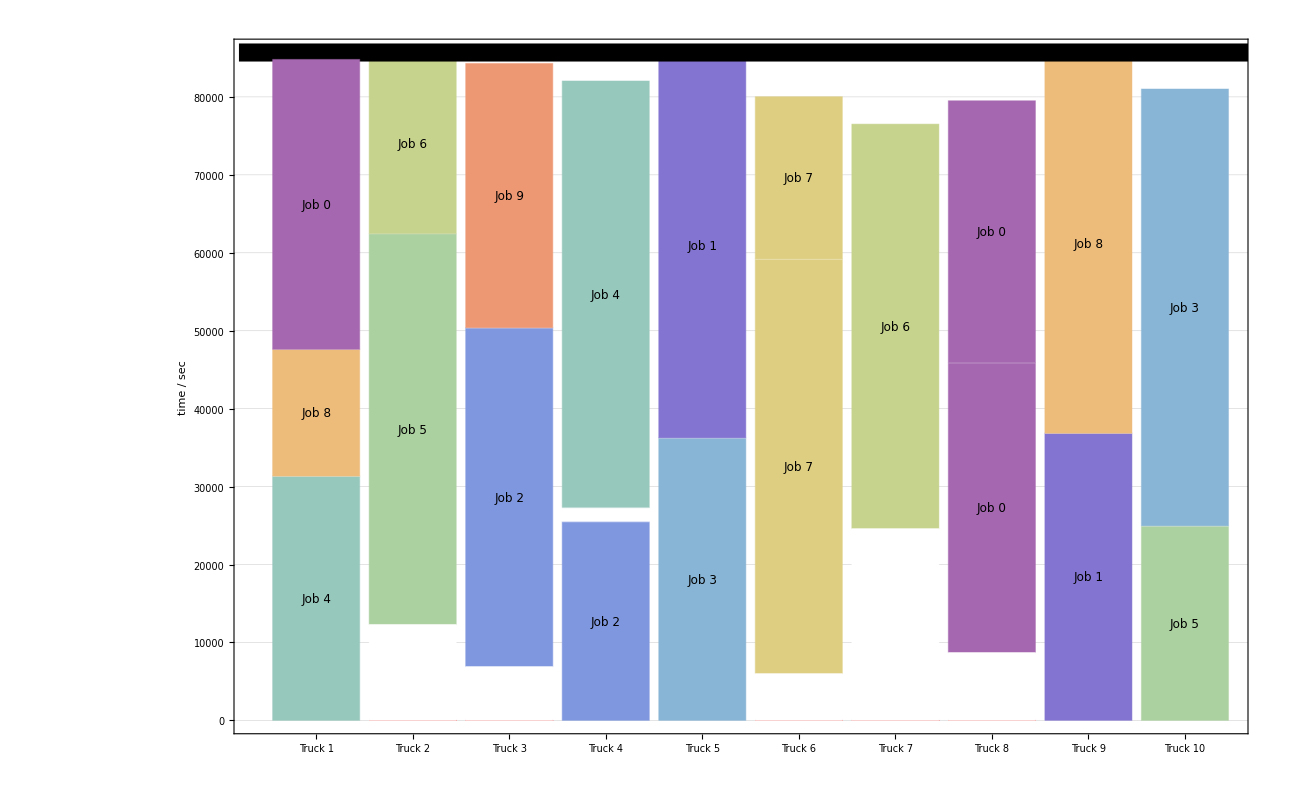

```mathematica
t5opt=PlotBarChart[t5,85690,10,1300,0.2,color, "Truck "]
```

## 3 Docks 10 Trucks

Inital Solution

```mathematica
d3init={{Style[Labeled[18600,Style["Truck 1",Black,12],Center],ColorData["BrightBands",0]],0,Style[Labeled[18600,Style["Truck 4",Black,12],Center],ColorData["BrightBands",0.3]],0,Style[Labeled[18600,Style["Truck 7",Black,12],Center],ColorData["BrightBands",0.6]],0,Style[Labeled[6000,Style["Truck 10",Black,12],Center],ColorData["BrightBands",0.9]],0,Style[Labeled[9600,Style["Truck 3",Black,12],Center],ColorData["BrightBands",0.2]],0,Style[Labeled[6900,Style["Truck 4",Black,12],Center],ColorData["BrightBands",0.3]],966,Style[Labeled[4200,Style["Truck 10",Black,12],Center],ColorData["BrightBands",0.9]],3176,Style[Labeled[2400,Style["Truck 8",Black,12],Center],ColorData["BrightBands",0.7]],2438,Style[Labeled[2400,Style["Truck 4",Black,12],Center],ColorData["BrightBands",0.3]]},{Style[Labeled[18600,Style["Truck 2",Black,12],Center],ColorData["BrightBands",0.1]],0,Style[Labeled[18600,Style["Truck 5",Black,12],Center],ColorData["BrightBands",0.4]],0,Style[Labeled[18600,Style["Truck 8",Black,12],Center],ColorData["BrightBands",0.7]],0,Style[Labeled[18600,Style["Truck 2",Black,12],Center],ColorData["BrightBands",0.1]],0,Style[Labeled[6000,Style["Truck 6",Black,12],Center],ColorData["BrightBands",0.5]],12960,Style[Labeled[16800,Style["Truck 1",Black,12],Center],ColorData["BrightBands",0]]},{Style[Labeled[18600,Style["Truck 3",Black,12],Center],ColorData["BrightBands",0.2]],0,Style[Labeled[18600,Style["Truck 6",Black,12],Center],ColorData["BrightBands",0.5]],0,Style[Labeled[18600,Style["Truck 9",Black,12],Center],ColorData["BrightBands",0.8]],0,Style[Labeled[12300,Style["Truck 1",Black,12],Center],ColorData["BrightBands",0]],0,Style[Labeled[8700,Style["Truck 5",Black,12],Center],ColorData["BrightBands",0.4]]}};
t3init={{Style[Labeled[54738,Style["Job 0",Black,12],Center],Lighter[ColorData["Rainbow",0]]],1062,Style[Labeled[37560,Style["Job 1",Black,12],Center],Lighter[ColorData["Rainbow",0.1]]],0,Style[Labeled[51138,Style["Job 0",Black,12],Center],Lighter[ColorData["Rainbow",0]]]},{Style[Labeled[50160,Style["Job 1",Black,12],Center],Lighter[ColorData["Rainbow",0.1]]],5640,Style[Labeled[54738,Style["Job 0",Black,12],Center],Lighter[ColorData["Rainbow",0]]]},{Style[Labeled[56048,Style["Job 2",Black,12],Center],Lighter[ColorData["Rainbow",0.2]]],5752,Style[Labeled[38048,Style["Job 2",Black,12],Center],Lighter[ColorData["Rainbow",0.2]]]},{0,18600,Style[Labeled[51902,Style["Job 3",Black,12],Center],Lighter[ColorData["Rainbow",0.3]]],898,Style[Labeled[20080,Style["Job 4",Black,12],Center],Lighter[ColorData["Rainbow",0.4]]],0,Style[Labeled[26704,Style["Job 8",Black,12],Center],Lighter[ColorData["Rainbow",0.8]]]},{0,18600,Style[Labeled[43480,Style["Job 4",Black,12],Center],Lighter[ColorData["Rainbow",0.4]]],6020,Style[Labeled[32102,Style["Job 3",Black,12],Center],Lighter[ColorData["Rainbow",0.3]]]},{0,18600,Style[Labeled[53210,Style["Job 5",Black,12],Center],Lighter[ColorData["Rainbow",0.5]]],2590,Style[Labeled[28010,Style["Job 5",Black,12],Center],Lighter[ColorData["Rainbow",0.5]]]},{0,37200,Style[Labeled[62330,Style["Job 6",Black,12],Center],Lighter[ColorData["Rainbow",0.6]]]},{0,37200,Style[Labeled[49442,Style["Job 7",Black,12],Center],Lighter[ColorData["Rainbow",0.7]]],0,Style[Labeled[17042,Style["Job 7",Black,12],Center],Lighter[ColorData["Rainbow",0.7]]]},{0,37200,Style[Labeled[59104,Style["Job 8",Black,12],Center],Lighter[ColorData["Rainbow",0.8]]]},{0,55800,Style[Labeled[23466,Style["Job 9",Black,12],Center],Lighter[ColorData["Rainbow",0.9]]],0,Style[Labeled[33530,Style["Job 6",Black,12],Center],Lighter[ColorData["Rainbow",0.6]]]}};
```

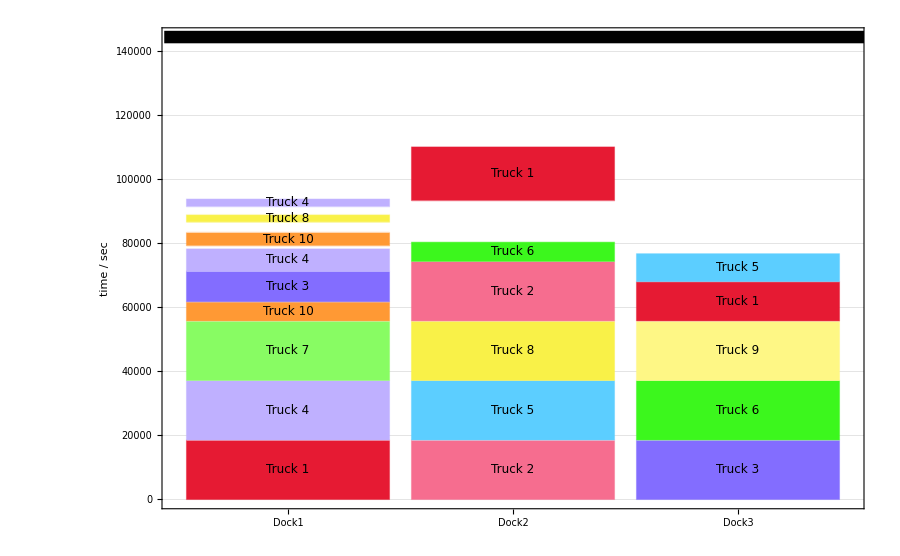

```mathematica
initd3=PlotBarChart[d3init,144498,3,900,0.45,color,"Dock",{0.5,3.5}]
```

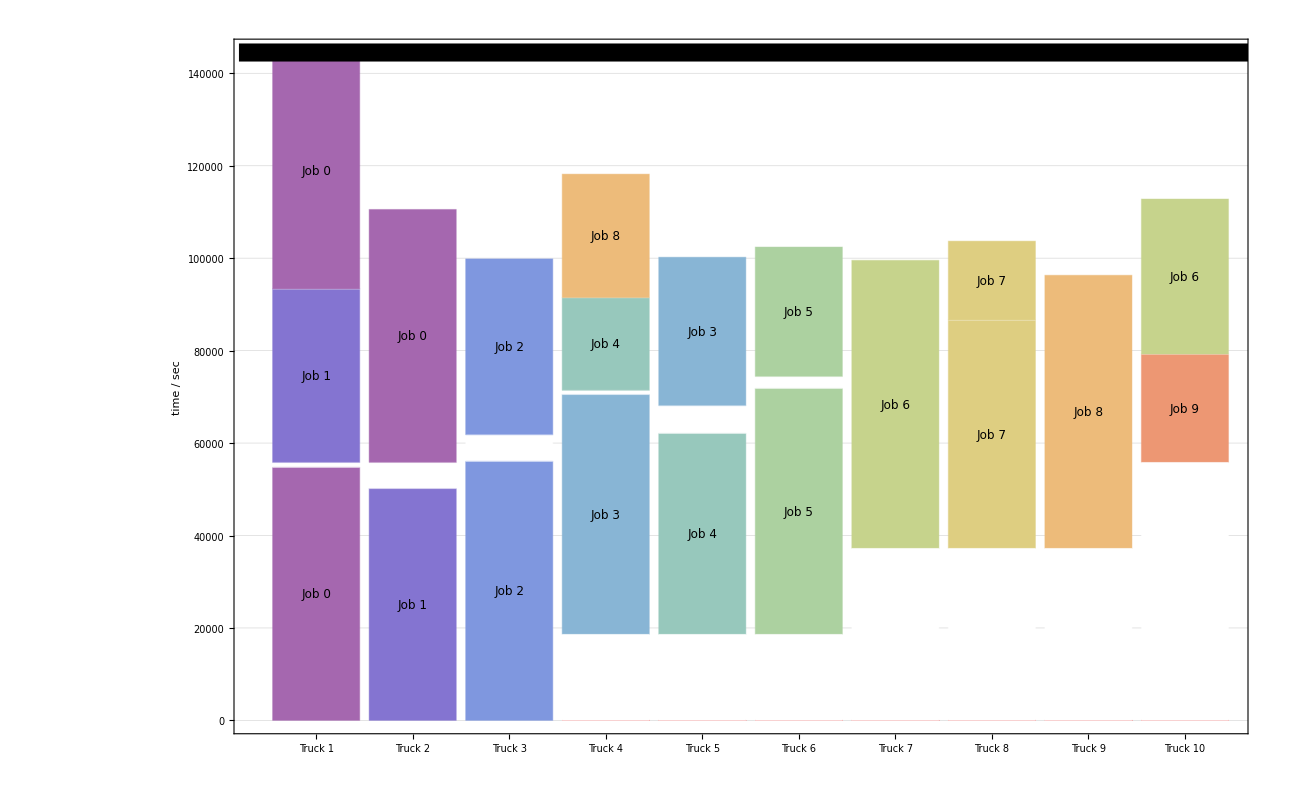

```mathematica
initt3=PlotBarChart[t3init,144498,10,1300,0.2,color, "Truck "]
```

3 Docks: VNDS Optimization with 1000 nsteps && 100 moves

```mathematica
d3={{Style[Labeled[2400,Style["Truck 4",Black,12],Center],ColorData["BrightBands",0.3]],0,Style[Labeled[18600,Style["Truck 10",Black,12],Center],ColorData["BrightBands",0.9]],0,Style[Labeled[8700,Style["Truck 2",Black,12],Center],ColorData["BrightBands",0.1]],0,Style[Labeled[18600,Style["Truck 4",Black,12],Center],ColorData["BrightBands",0.3]],0,Style[Labeled[18600,Style["Truck 6",Black,12],Center],ColorData["BrightBands",0.5]],0,Style[Labeled[12300,Style["Truck 2",Black,12],Center],ColorData["BrightBands",0.1]],0,Style[Labeled[9600,Style["Truck 4",Black,12],Center],ColorData["BrightBands",0.3]]},{Style[Labeled[2400,Style["Truck 1",Black,12],Center],ColorData["BrightBands",0]],0,Style[Labeled[18600,Style["Truck 8",Black,12],Center],ColorData["BrightBands",0.7]],0,Style[Labeled[6000,Style["Truck 5",Black,12],Center],ColorData["BrightBands",0.4]],0,Style[Labeled[18600,Style["Truck 3",Black,12],Center],ColorData["BrightBands",0.2]],0,Style[Labeled[16800,Style["Truck 1",Black,12],Center],ColorData["BrightBands",0]],0,Style[Labeled[18600,Style["Truck 8",Black,12],Center],ColorData["BrightBands",0.7]],0,Style[Labeled[4200,Style["Truck 1",Black,12],Center],ColorData["BrightBands",0]]},{Style[Labeled[18600,Style["Truck 6",Black,12],Center],ColorData["BrightBands",0.5]],0,Style[Labeled[18600,Style["Truck 9",Black,12],Center],ColorData["BrightBands",0.8]],0,Style[Labeled[18600,Style["Truck 7",Black,12],Center],ColorData["BrightBands",0.6]],0,Style[Labeled[18600,Style["Truck 10",Black,12],Center],ColorData["BrightBands",0.9]],0,Style[Labeled[6900,Style["Truck 5",Black,12],Center],ColorData["BrightBands",0.4]],0,Style[Labeled[6000,Style["Truck 3",Black,12],Center],ColorData["BrightBands",0.2]]}};
t3={{Style[Labeled[16266,Style["Job 8",Black,12],Center],Lighter[ColorData["Rainbow",0.8]]],29334,Style[Labeled[33600,Style["Job 0",Black,12],Center],Lighter[ColorData["Rainbow",0]]],1800,Style[Labeled[23102,Style["Job 6",Black,12],Center],Lighter[ColorData["Rainbow",0.6]]]},{0,21000,Style[Labeled[36248,Style["Job 3",Black,12],Center],Lighter[ColorData["Rainbow",0.3]]],9652,Style[Labeled[36842,Style["Job 1",Black,12],Center],Lighter[ColorData["Rainbow",0.1]]]},{0,27000,Style[Labeled[49442,Style["Job 1",Black,12],Center],Lighter[ColorData["Rainbow",0.1]]],4858,Style[Labeled[24960,Style["Job 5",Black,12],Center],Lighter[ColorData["Rainbow",0.5]]]},{Style[Labeled[20810,Style["Job 7",Black,12],Center],Lighter[ColorData["Rainbow",0.7]]],8890,Style[Labeled[37200,Style["Job 0",Black,12],Center],Lighter[ColorData["Rainbow",0]]],12300,Style[Labeled[25480,Style["Job 2",Black,12],Center],Lighter[ColorData["Rainbow",0.2]]]},{0,21000,Style[Labeled[33904,Style["Job 9",Black,12],Center],Lighter[ColorData["Rainbow",0.9]]],19496,Style[Labeled[31338,Style["Job 4",Black,12],Center],Lighter[ColorData["Rainbow",0.4]]]},{Style[Labeled[43480,Style["Job 2",Black,12],Center],Lighter[ColorData["Rainbow",0.2]]],4820,Style[Labeled[56048,Style["Job 3",Black,12],Center],Lighter[ColorData["Rainbow",0.3]]]},{0,37200,Style[Labeled[48666,Style["Job 8",Black,12],Center],Lighter[ColorData["Rainbow",0.8]]]},{0,2400,Style[Labeled[53210,Style["Job 7",Black,12],Center],Lighter[ColorData["Rainbow",0.7]]],6790,Style[Labeled[37200,Style["Job 0",Black,12],Center],Lighter[ColorData["Rainbow",0]]]},{0,18600,Style[Labeled[54738,Style["Job 4",Black,12],Center],Lighter[ColorData["Rainbow",0.4]]]},{0,2400,Style[Labeled[51902,Style["Job 6",Black,12],Center],Lighter[ColorData["Rainbow",0.6]]],1498,Style[Labeled[50160,Style["Job 5",Black,12],Center],Lighter[ColorData["Rainbow",0.5]]]}};
```

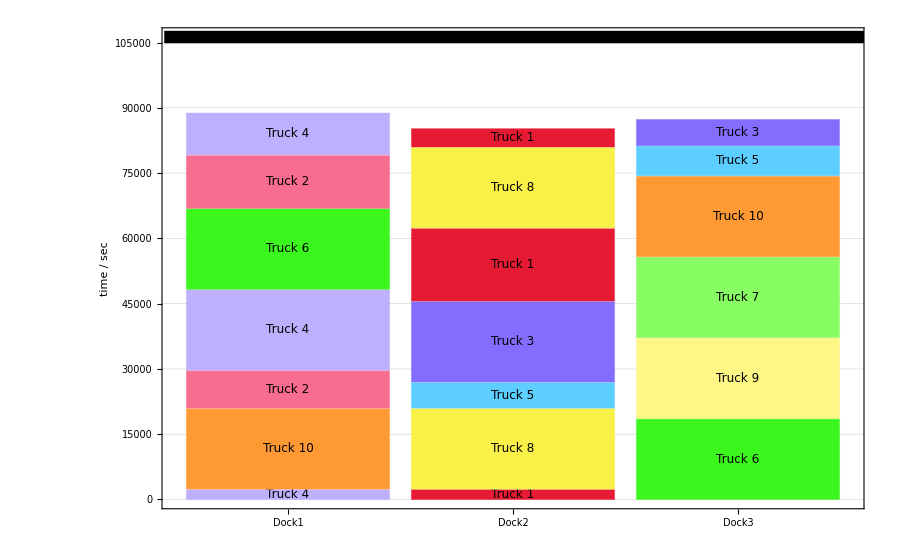

```mathematica
optd3=PlotBarChart[d3,106260,3,900,0.45,color,"Dock",{0.5,3.5}]
```

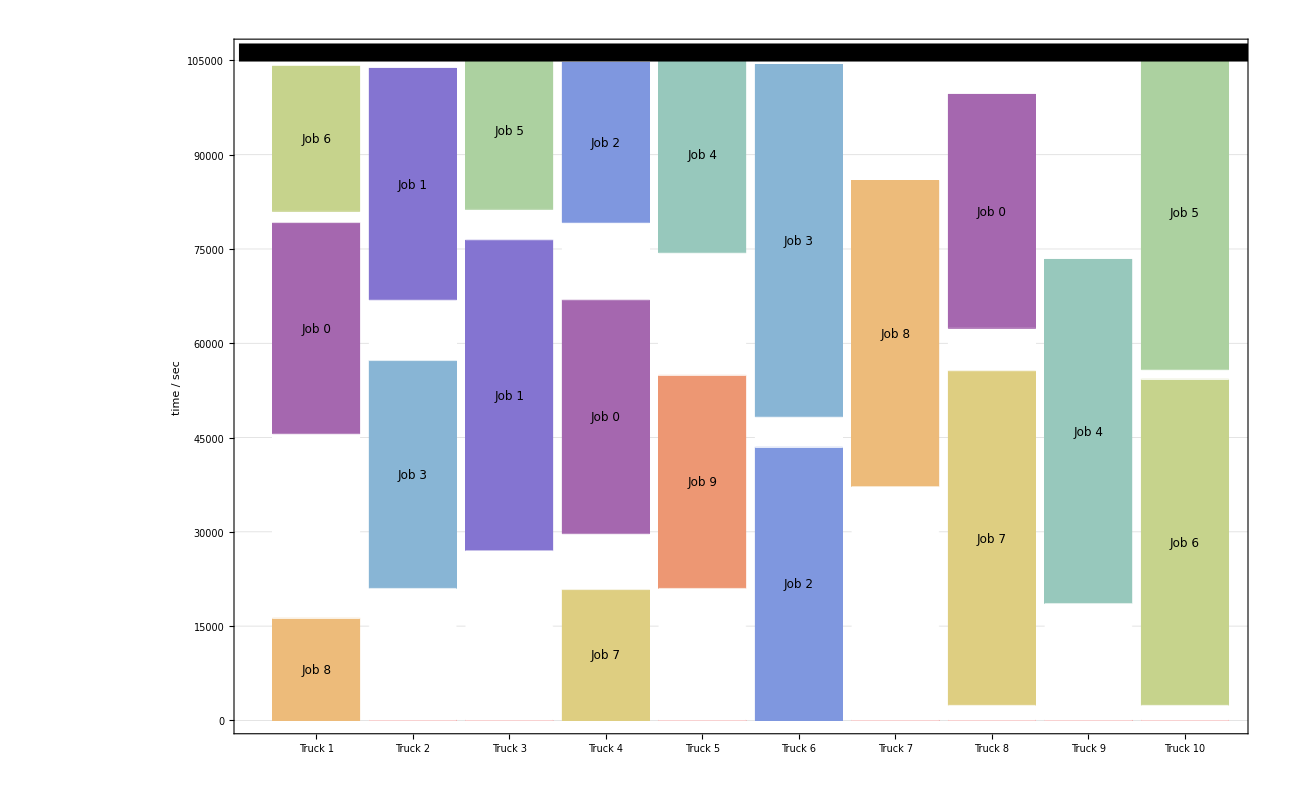

```mathematica
optt3=PlotBarChart[t3,106260,10,1300,0.2,color, "Truck "]
```

## 8 Docks 10 Trucks

Inital Solution

```mathematica
d8init={{Style[Labeled[18600,Style["Truck 1",Black,12],Center],ColorData["BrightBands",0]],0,Style[Labeled[18600,Style["Truck 9",Black,12],Center],ColorData["BrightBands",0.8]],4866,Style[Labeled[18600,Style["Truck 10",Black,12],Center],ColorData["BrightBands",0.9]],1664,Style[Labeled[2400,Style["Truck 7",Black,12],Center],ColorData["BrightBands",0.6]],7252,Style[Labeled[16800,Style["Truck 4",Black,12],Center],ColorData["BrightBands",0.3]]},{Style[Labeled[18600,Style["Truck 2",Black,12],Center],ColorData["BrightBands",0.1]],0,Style[Labeled[6000,Style["Truck 10",Black,12],Center],ColorData["BrightBands",0.9]],18880,Style[Labeled[12300,Style["Truck 5",Black,12],Center],ColorData["BrightBands",0.4]],268,Style[Labeled[2400,Style["Truck 3",Black,12],Center],ColorData["BrightBands",0.2]]},{Style[Labeled[18600,Style["Truck 3",Black,12],Center],ColorData["BrightBands",0.2]],30842,Style[Labeled[9600,Style["Truck 8",Black,12],Center],ColorData["BrightBands",0.7]]},{Style[Labeled[18600,Style["Truck 4",Black,12],Center],ColorData["BrightBands",0.3]],31560,Style[Labeled[8700,Style["Truck 2",Black,12],Center],ColorData["BrightBands",0.1]]},{Style[Labeled[18600,Style["Truck 5",Black,12],Center],ColorData["BrightBands",0.4]],33302,Style[Labeled[6900,Style["Truck 4",Black,12],Center],ColorData["BrightBands",0.3]]},{Style[Labeled[18600,Style["Truck 6",Black,12],Center],ColorData["BrightBands",0.5]],34610,Style[Labeled[6000,Style["Truck 6",Black,12],Center],ColorData["BrightBands",0.5]]},{Style[Labeled[18600,Style["Truck 7",Black,12],Center],ColorData["BrightBands",0.6]],36138,Style[Labeled[4200,Style["Truck 1",Black,12],Center],ColorData["BrightBands",0]]},{Style[Labeled[18600,Style["Truck 8",Black,12],Center],ColorData["BrightBands",0.7]]}};

t8init={{Style[Labeled[54738,Style["Job 0",Black,12],Center],Lighter[ColorData["Rainbow",0]]],0,Style[Labeled[33530,Style["Job 6",Black,12],Center],Lighter[ColorData["Rainbow",0.6]]]},{Style[Labeled[50160,Style["Job 1",Black,12],Center],Lighter[ColorData["Rainbow",0.1]]],0,Style[Labeled[32102,Style["Job 3",Black,12],Center],Lighter[ColorData["Rainbow",0.3]]]},{Style[Labeled[56048,Style["Job 2",Black,12],Center],Lighter[ColorData["Rainbow",0.2]]],0,Style[Labeled[17042,Style["Job 7",Black,12],Center],Lighter[ColorData["Rainbow",0.7]]]},{Style[Labeled[51902,Style["Job 3",Black,12],Center],Lighter[ColorData["Rainbow",0.3]]],0,Style[Labeled[20080,Style["Job 4",Black,12],Center],Lighter[ColorData["Rainbow",0.4]]],0,Style[Labeled[51138,Style["Job 0",Black,12],Center],Lighter[ColorData["Rainbow",0]]]},{Style[Labeled[43480,Style["Job 4",Black,12],Center],Lighter[ColorData["Rainbow",0.4]]],0,Style[Labeled[37560,Style["Job 1",Black,12],Center],Lighter[ColorData["Rainbow",0.1]]]},{Style[Labeled[53210,Style["Job 5",Black,12],Center],Lighter[ColorData["Rainbow",0.5]]],0,Style[Labeled[28010,Style["Job 5",Black,12],Center],Lighter[ColorData["Rainbow",0.5]]]},{Style[Labeled[62330,Style["Job 6",Black,12],Center],Lighter[ColorData["Rainbow",0.6]]],0,Style[Labeled[26704,Style["Job 8",Black,12],Center],Lighter[ColorData["Rainbow",0.8]]]},{Style[Labeled[49442,Style["Job 7",Black,12],Center],Lighter[ColorData["Rainbow",0.7]]],0,Style[Labeled[38048,Style["Job 2",Black,12],Center],Lighter[ColorData["Rainbow",0.2]]]},{0,18600,Style[Labeled[59104,Style["Job 8",Black,12],Center],Lighter[ColorData["Rainbow",0.8]]]},{0,18600,Style[Labeled[23466,Style["Job 9",Black,12],Center],Lighter[ColorData["Rainbow",0.9]]],0,Style[Labeled[54738,Style["Job 0",Black,12],Center],Lighter[ColorData["Rainbow",0]]]}};
```

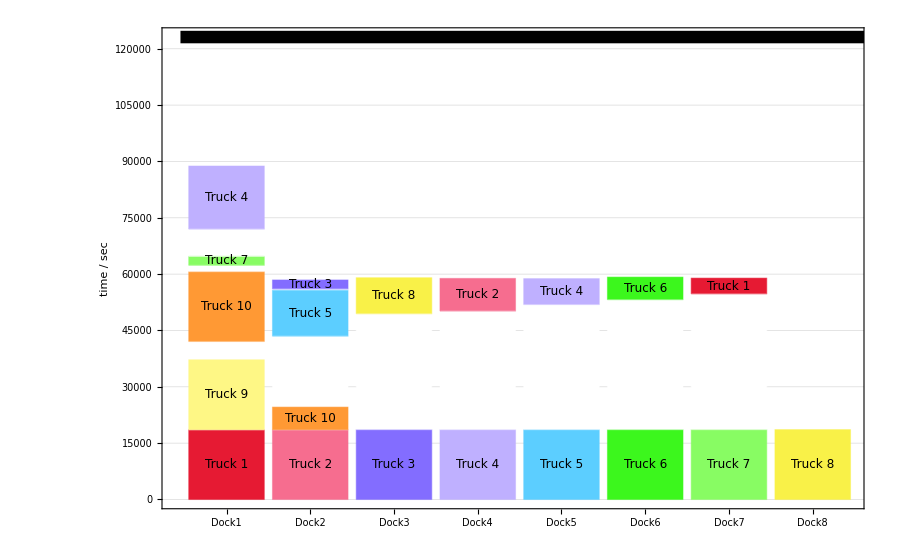

```mathematica
initd8=PlotBarChart[d8init,123120,8,900,0.45,color,"Dock"]
```

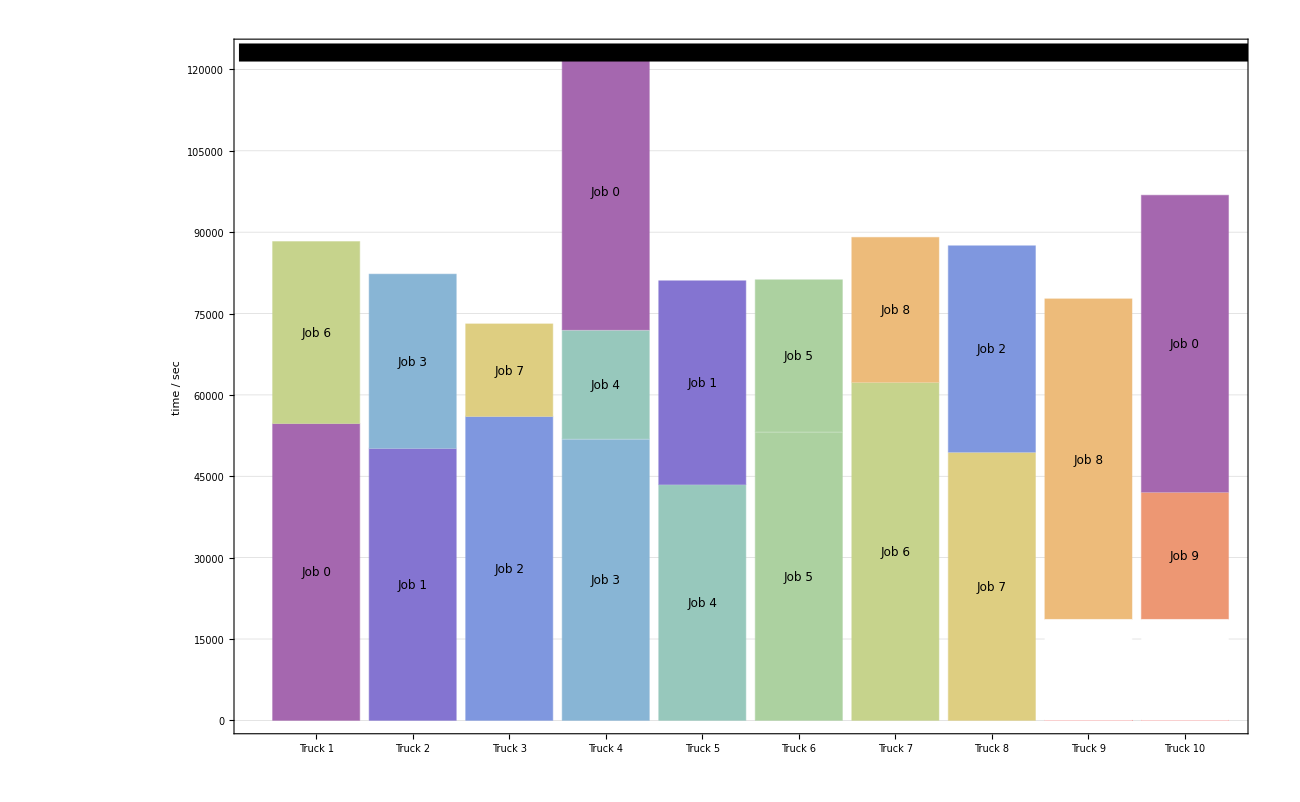

```mathematica
initt8=PlotBarChart[t8init,123120,10,1300,0.2,color, "Truck "]
```

8 Docks: VNDS Optimization with 1000 nsteps && 100 moves

```mathematica
d8={{Style[Labeled[2400,Style["Truck 4",Black,12],Center],ColorData["BrightBands",0.3]],0,Style[Labeled[2400,Style["Truck 8",Black,12],Center],ColorData["BrightBands",0.7]],0,Style[Labeled[18600,Style["Truck 9",Black,12],Center],ColorData["BrightBands",0.8]],1560,Style[Labeled[18600,Style["Truck 6",Black,12],Center],ColorData["BrightBands",0.5]],11178,Style[Labeled[4200,Style["Truck 7",Black,12],Center],ColorData["BrightBands",0.6]]},{Style[Labeled[8700,Style["Truck 10",Black,12],Center],ColorData["BrightBands",0.9]],7566,Style[Labeled[18600,Style["Truck 4",Black,12],Center],ColorData["BrightBands",0.3]],1976,Style[Labeled[18600,Style["Truck 2",Black,12],Center],ColorData["BrightBands",0.1]]},{Style[Labeled[18600,Style["Truck 1",Black,12],Center],ColorData["BrightBands",0]],4610,Style[Labeled[18600,Style["Truck 8",Black,12],Center],ColorData["BrightBands",0.7]]},{Style[Labeled[6000,Style["Truck 5",Black,12],Center],ColorData["BrightBands",0.4]],43442,Style[Labeled[16800,Style["Truck 1",Black,12],Center],ColorData["BrightBands",0]]},{Style[Labeled[18600,Style["Truck 7",Black,12],Center],ColorData["BrightBands",0.6]],12738,Style[Labeled[18600,Style["Truck 3",Black,12],Center],ColorData["BrightBands",0.2]]},{Style[Labeled[6900,Style["Truck 3",Black,12],Center],ColorData["BrightBands",0.2]],29348,Style[Labeled[18600,Style["Truck 10",Black,12],Center],ColorData["BrightBands",0.9]]},{Style[Labeled[12300,Style["Truck 2",Black,12],Center],ColorData["BrightBands",0.1]],41166,Style[Labeled[9600,Style["Truck 4",Black,12],Center],ColorData["BrightBands",0.3]]},{Style[Labeled[6000,Style["Truck 6",Black,12],Center],ColorData["BrightBands",0.5]],27904,Style[Labeled[18600,Style["Truck 5",Black,12],Center],ColorData["BrightBands",0.4]]}};
t8={{Style[Labeled[49442,Style["Job 1",Black,12],Center],Lighter[ColorData["Rainbow",0.1]]],0,Style[Labeled[33600,Style["Job 0",Black,12],Center],Lighter[ColorData["Rainbow",0]]]},{Style[Labeled[36842,Style["Job 1",Black,12],Center],Lighter[ColorData["Rainbow",0.1]]],0,Style[Labeled[37200,Style["Job 0",Black,12],Center],Lighter[ColorData["Rainbow",0]]]},{Style[Labeled[31338,Style["Job 4",Black,12],Center],Lighter[ColorData["Rainbow",0.4]]],0,Style[Labeled[50160,Style["Job 5",Black,12],Center],Lighter[ColorData["Rainbow",0.5]]]},{Style[Labeled[16266,Style["Job 8",Black,12],Center],Lighter[ColorData["Rainbow",0.8]]],0,Style[Labeled[37200,Style["Job 0",Black,12],Center],Lighter[ColorData["Rainbow",0]]],0,Style[Labeled[25480,Style["Job 2",Black,12],Center],Lighter[ColorData["Rainbow",0.2]]]},{Style[Labeled[33904,Style["Job 9",Black,12],Center],Lighter[ColorData["Rainbow",0.9]]],0,Style[Labeled[48666,Style["Job 8",Black,12],Center],Lighter[ColorData["Rainbow",0.8]]]},{Style[Labeled[24960,Style["Job 5",Black,12],Center],Lighter[ColorData["Rainbow",0.5]]],0,Style[Labeled[56048,Style["Job 3",Black,12],Center],Lighter[ColorData["Rainbow",0.3]]]},{Style[Labeled[54738,Style["Job 4",Black,12],Center],Lighter[ColorData["Rainbow",0.4]]],0,Style[Labeled[23102,Style["Job 6",Black,12],Center],Lighter[ColorData["Rainbow",0.6]]]},{0,2400,Style[Labeled[20810,Style["Job 7",Black,12],Center],Lighter[ColorData["Rainbow",0.7]]],0,Style[Labeled[51902,Style["Job 6",Black,12],Center],Lighter[ColorData["Rainbow",0.6]]]},{0,4800,Style[Labeled[53210,Style["Job 7",Black,12],Center],Lighter[ColorData["Rainbow",0.7]]]},{Style[Labeled[36248,Style["Job 3",Black,12],Center],Lighter[ColorData["Rainbow",0.3]]],0,Style[Labeled[43480,Style["Job 2",Black,12],Center],Lighter[ColorData["Rainbow",0.2]]]}};
```

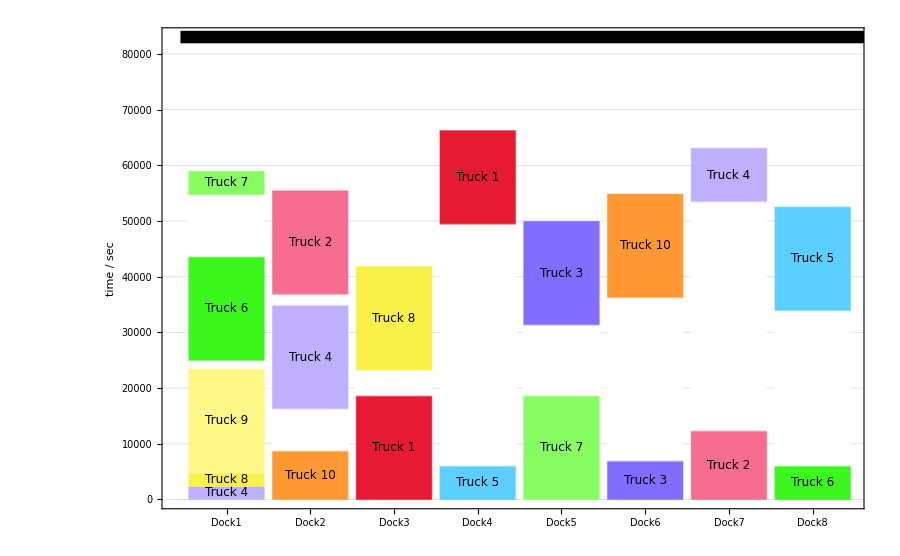

```mathematica
optd8=PlotBarChart[d8,83042,8,900,0.45,color,"Dock"]
```

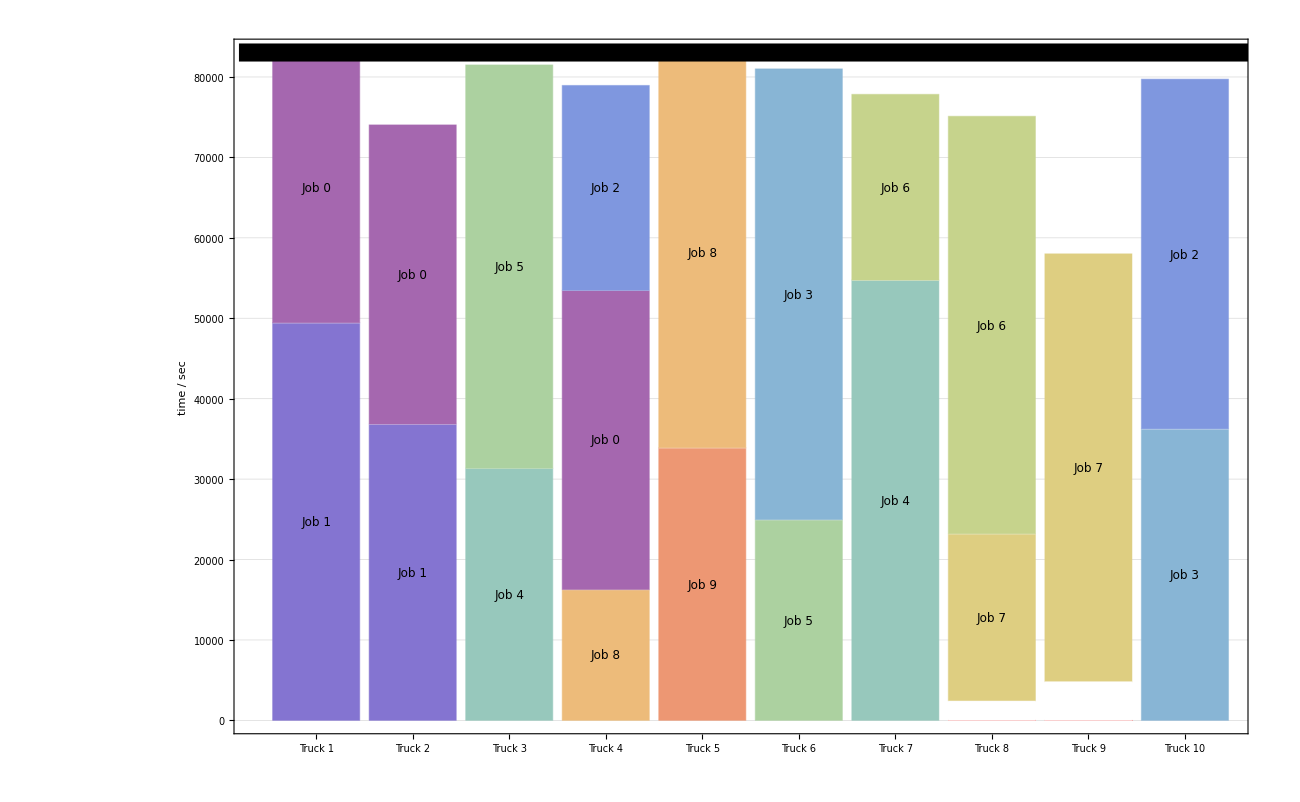

```mathematica
optt8=PlotBarChart[t8,83042,10,1300,0.2,color, "Truck "]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/lindorfer/ReWiTech/Masterarbeit/Programs/Daten_Simplified_A

```mathematica
Export["init5.pdf",init]
Export["inittrucks.pdf",inittrucks]
```

init5.pdf

inittrucks.pdf

```mathematica
Export["opt5.pdf",d5opt]
Export["optt5.pdf",t5opt]
```

opt5.pdf

optt5.pdf

```mathematica
Export["init3.pdf",initd3]
Export["initt3.pdf",initt3]
```

init3.pdf

initt3.pdf

```mathematica
Export["opt3.pdf",optd3]
Export["optt3.pdf",optt3]
```

opt3.pdf

optt3.pdf

```mathematica
Export["init8.pdf",initd8]
Export["initt8.pdf",initt8]
```

init8.pdf

initt8.pdf

```mathematica
Export["opt8.pdf",optd8]
Export["optt8.pdf",optt8]
```

opt8.pdf

optt8.pdf

## Plot the test - set

```mathematica
SetDirectory["/home/lindorfer/ReWiTech/Masterarbeit/Programs/Daten_Simplified_A"]
```

/home/lindorfer/ReWiTech/Masterarbeit/Programs/Daten_Simplified_A

```mathematica
coords=Import["TravelTim1_test.dat"]
```

{{12602,5915},{11746,11976},{13674,2963},{5028,11523},{4166,8309},{7160,9433},{5471,7701},{14283,13742},{9535,10759},{2124,9104},{244,3643}}

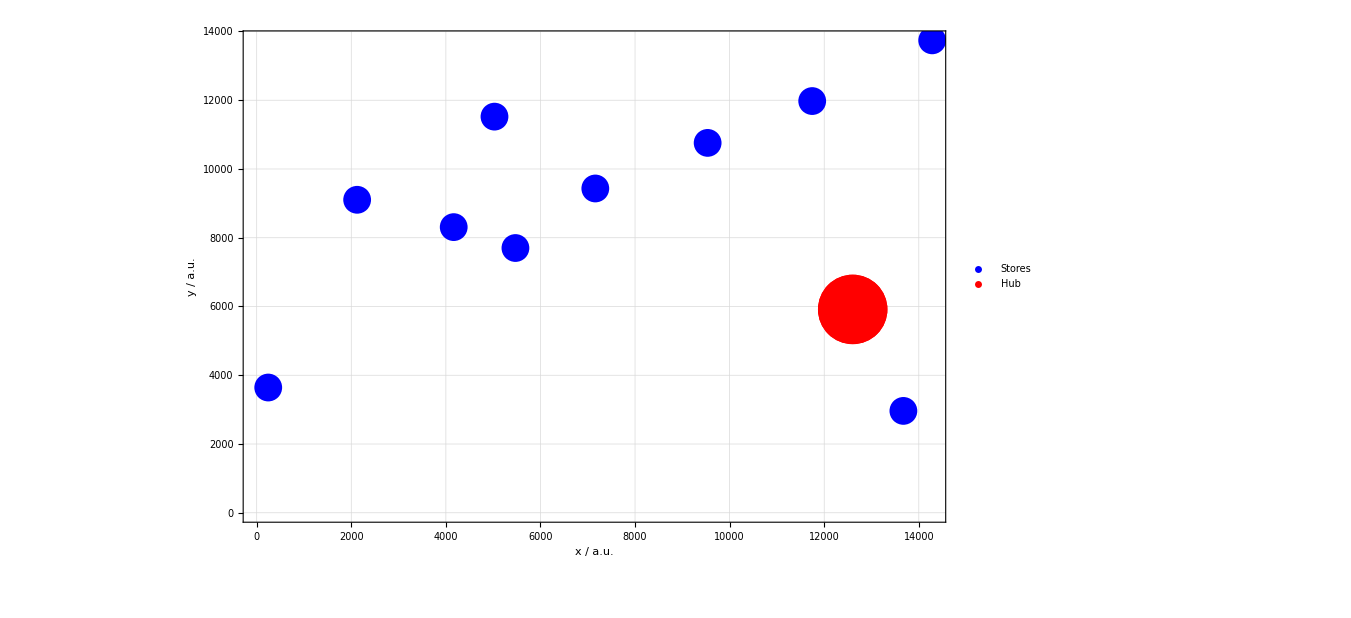

```mathematica
graph=ListPlot[{coords,{{12602,5915}}},
Frame->True,
LabelStyle->{30,Black},
FrameLabel->{{"y / a.u.",None},{"x / a.u.",None}},
LabelStyle->25,
PlotStyle->{{PointSize[0.02],Blue},{PointSize[0.07],Red}},
PlotTheme->{"Classic","Detailed"},
ImageSize->1000,
PlotLegends->Placed[{"Stores","Hub"},Above]]
```

```mathematica
Export["Graph.pdf",graph]
```

Graph.pdf

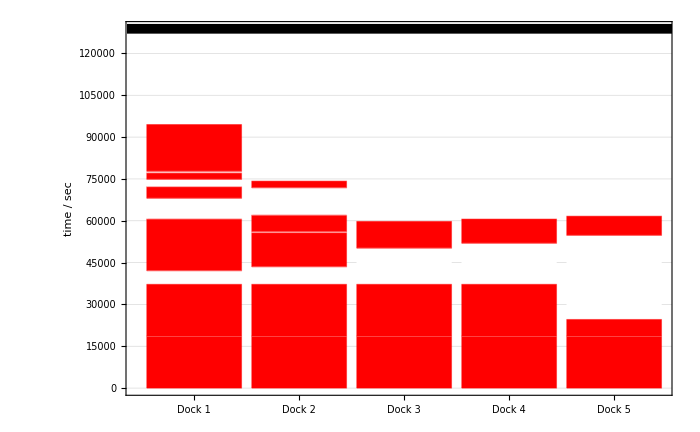

```mathematica
init=PlotBarChart[t1,128842,5,700,0.36]
```

```mathematica
Export["InitialSol.pdf",init]
```

InitialSol.pdf

```mathematica
diffDockSize={{2,179818},{2,147600},{3,144498},{3,106260},{4,135420},{4,90066},{5,128842},{5,85690},{6,128842},{6,83042},{7,124428},{7,83042},{8,123120},{8,83042}};
```

```mathematica
AppendTo[$Path,"/home/lindorfer/LevelScheme"]
```

{/home/lindorfer/.Mathematica/DocumentationIndices,/usr/local/Wolfram/Mathematica/12.0/SystemFiles/Links,/home/lindorfer/.Mathematica/Kernel,/home/lindorfer/.Mathematica/Autoload,/home/lindorfer/.Mathematica/Applications,/usr/share/Mathematica/Kernel,/usr/share/Mathematica/Autoload,/usr/share/Mathematica/Applications,.,/home/lindorfer,/usr/local/Wolfram/Mathematica/12.0/AddOns/Packages,/usr/local/Wolfram/Mathematica/12.0/SystemFiles/Autoload,/usr/local/Wolfram/Mathematica/12.0/AddOns/Autoload,/usr/local/Wolfram/Mathematica/12.0/AddOns/Applications,/usr/local/Wolfram/Mathematica/12.0/AddOns/ExtraPackages,/usr/local/Wolfram/Mathematica/12.0/SystemFiles/Kernel/Packages,/usr/local/Wolfram/Mathematica/12.0/Documentation/English/System,/usr/local/Wolfram/Mathematica/12.0/SystemFiles/Data/ICC,/home/lindorfer/LevelScheme,/home/lindorfer/LevelScheme}

```mathematica
$Path
```

{/home/lindorfer/.Mathematica/DocumentationIndices,/usr/local/Wolfram/Mathematica/12.0/SystemFiles/Links,/home/lindorfer/.Mathematica/Kernel,/home/lindorfer/.Mathematica/Autoload,/home/lindorfer/.Mathematica/Applications,/usr/share/Mathematica/Kernel,/usr/share/Mathematica/Autoload,/usr/share/Mathematica/Applications,.,/home/lindorfer,/usr/local/Wolfram/Mathematica/12.0/AddOns/Packages,/usr/local/Wolfram/Mathematica/12.0/SystemFiles/Autoload,/usr/local/Wolfram/Mathematica/12.0/AddOns/Autoload,/usr/local/Wolfram/Mathematica/12.0/AddOns/Applications,/usr/local/Wolfram/Mathematica/12.0/AddOns/ExtraPackages,/usr/local/Wolfram/Mathematica/12.0/SystemFiles/Kernel/Packages,/usr/local/Wolfram/Mathematica/12.0/Documentation/English/System,/usr/local/Wolfram/Mathematica/12.0/SystemFiles/Data/ICC,/home/lindorfer/LevelScheme,/home/lindorfer/LevelScheme}

```mathematica
<<StylePlot.m
```

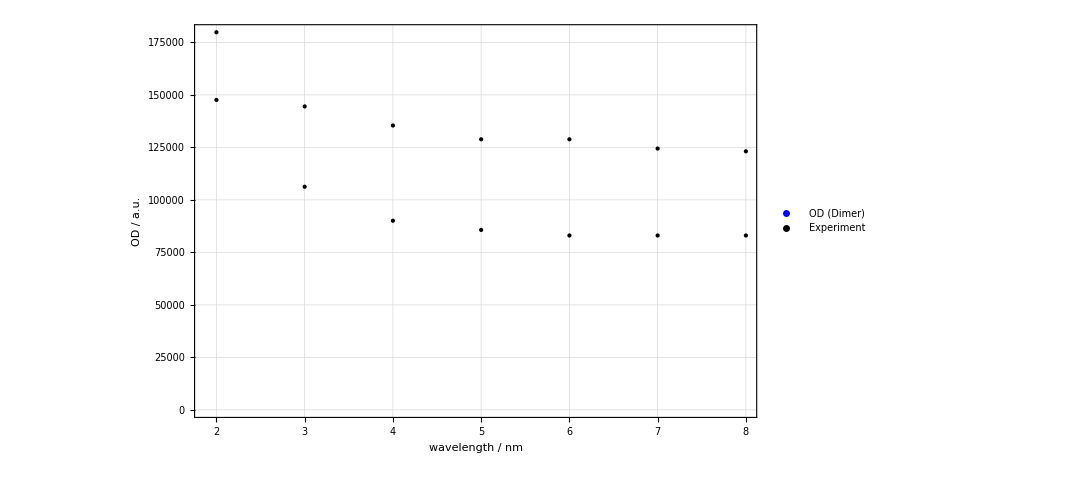

```mathematica
StyleListPlot[diffDockSize,

PlotStyle->{{Black,Thickness[0.008]},{Blue,Dashing[0.023],Thickness[0.008]},{Red,Dashing[{0,0.03,0.03,0.03}],Thickness[0.008]},{Purple,Thickness[0.008]}},

Joined->False,
PlotRange->{All,All},
FrameLabels->{{"OD / a.u.",""},{"wavelength / nm",""}},
LegendText->Map[Style[#,{Bold,FontFamily->"Helvetica"}]&,{"OD (Dimer)","Experiment"}],
LegendPlacement->{{0.2,0.22}},
PlotMarkers->None,
PlotLegendsLineColor->{Directive[Blue,AbsoluteThickness[5],Dashing[0.028]],Directive[Black,AbsoluteThickness[5]]},
GridLinesStyle->Directive[Gray, Dashed]
]
```

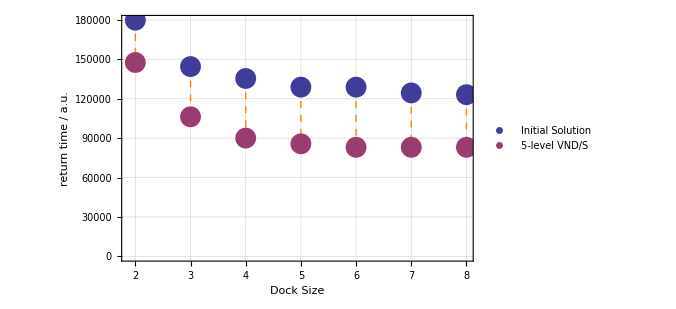

```mathematica
diffdocks=ListPlot[{{{2,179818},{3,144498},{4,135420},{5,128842},{6,128842},{7,124428},{8,123120}},{{2,147600},{3,106260},{4,90066},{5,85690},{6,83042},{7,83042},{8,83042}}},
PlotTheme->{"Detailed","Classic"},
FrameLabel->{{Style["return time  / a.u.",Black],None},{Style["Dock Size",Black],None}},
PlotStyle->PointSize[0.03],
FrameStyle->20,
LabelStyle->{FontFamily->"Arial",FontSize->13},
Frame->True,
ImageSize->500,
Filling->{1->{{2},Directive[Orange,Dashed]}},
PlotLegends->Placed[LineLegend[{"Initial Solution","5-level VND/S"},LegendFunction->(Framed[#,Background->White]&)],{{0.23,0.23}}]]
```

```mathematica
Export["ReturnTimes.pdf",diffdocks]
```

ReturnTimes.pdf

```mathematica
Directory[]
```

/home/lindorfer/ReWiTech/Masterarbeit/Programs/Daten_Simplified_A

```mathematica
PlotLegends->Placed[{"Initial Solution","5-level VND/S"},{{0.23,0.23}},LegendFunction->(Framed[#,Background->White]&)]
```

```mathematica
diffDockSize
```

{{2,179818},{2,147600},{3,144498},{3,106260},{4,135420},{4,90066},{5,128842},{5,85690},{6,128842},{6,83042},{7,124428},{7,83042},{8,123120},{8,83042}}